# Unanticipated consequences of spillover reduction

## Scott L. Nuismer December 12, 2023

## Mathematical Model and Solutions

## Set output path

```mathematica
HomePath="InsertPathHere";
```

## Notes

Because the focus is on humans, this notebook works in time units of years

## Age-independent steady-state solutions

```mathematica
Ṡ=b-λ S-δ S+ω R
```

b-S δ-S λ+R ω

```mathematica
Ι̇=λ S-γ Ι-δ Ι-μ Ι
```

-γ Ι-δ Ι+S λ-Ι μ

```mathematica
Ṁ=μ Ι-γ M-δ M-v M
```

-M v-M γ-M δ+Ι μ

```mathematica
Ṙ=γ Ι+γ M-δ R-ω R
```

M γ-R δ+γ Ι-R ω

### Generic equilibrium state

```mathematica
SimpEq=FullSimplify[Solve[{0==b-λ S-δ S+ω R,0==λ S-γ Ι-δ Ι-μ Ι,0==μ Ι-γ M-δ M-v M,0==γ Ι+γ M-δ R-ω R},{S,Ι,M,R}]]
```

{{S→(b (v+γ+δ) (γ+δ+μ) (δ+ω))/(δ (γ+δ+μ) ((δ+λ) (δ+ω)+γ (δ+λ+ω))+v ((δ+λ) (δ+μ) (δ+ω)+γ δ (δ+λ+ω))),Ι→-(b (v+γ+δ) λ (δ+ω))/(γ λ μ ω-(v+γ+δ) ((δ+λ) (δ+μ) (δ+ω)+γ δ (δ+λ+ω))),M→(b λ μ (δ+ω))/(δ (γ+δ+μ) ((δ+λ) (δ+ω)+γ (δ+λ+ω))+v ((δ+λ) (δ+μ) (δ+ω)+γ δ (δ+λ+ω))),R→(b γ λ (v+γ+δ+μ))/(δ (γ+δ+μ) ((δ+λ) (δ+ω)+γ (δ+λ+ω))+v ((δ+λ) (δ+μ) (δ+ω)+γ δ (δ+λ+ω)))}}

Total population size at steady state:

```mathematica
FullSimplify[(S+Ι+M+R)/.SimpEq]
```

{(b ((γ+δ+μ) ((δ+λ) (δ+ω)+γ (δ+λ+ω))+v ((δ+λ+μ) (δ+ω)+γ (δ+λ+ω))))/(δ (γ+δ+μ) ((δ+λ) (δ+ω)+γ (δ+λ+ω))+v ((δ+λ) (δ+μ) (δ+ω)+γ δ (δ+λ+ω)))}

```mathematica
TPS={Ν->(b ((γ+δ+μ) ((δ+λ) (δ+ω)+γ (δ+λ+ω))+v ((δ+λ+μ) (δ+ω)+γ (δ+λ+ω))))/(δ (γ+δ+μ) ((δ+λ) (δ+ω)+γ (δ+λ+ω))+v ((δ+λ) (δ+μ) (δ+ω)+γ δ (δ+λ+ω)))};
```

### Seroprevalence at Equilibrium

```mathematica
SeroP=FullSimplify[R/Ν/.SimpEq/.TPS]
```

{(γ λ (v+γ+δ+μ))/((γ+δ+μ) ((δ+λ) (δ+ω)+γ (δ+λ+ω))+v ((δ+λ+μ) (δ+ω)+γ (δ+λ+ω)))}

### Invert to find λ

```mathematica
FullSimplify[Solve[SeroP==ℛ,λ]]
```

{}

## Some useful calculations and transformations

### Proportion of population in the M class our approximations neglect

```mathematica
PropM=FullSimplify[M/(S+Ι+M+R)/.SimpEq]
```

{(λ μ (δ+ω))/((γ+δ+μ) ((δ+λ) (δ+ω)+γ (δ+λ+ω))+v ((δ+λ+μ) (δ+ω)+γ (δ+λ+ω)))}

```mathematica
Pars={b->100,μ->10,γ->1/(7/365),δ->1/60,v->0,λ->.1};
```

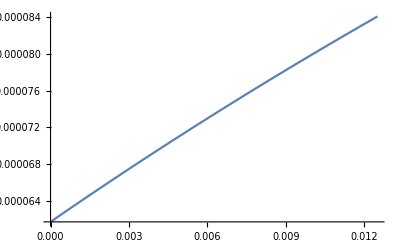

```mathematica
Plot[PropM/.Pars,{ω,0,1/80}]
```

The proportion of individuals in the M class rises with the rate at which immunity wanes. This is consistent with the observation that our approximation is less accurate in the presence of waning immunity.

### Relating probability of developing symptoms to the parameter μ

Over the course of the infection, then, what is the probability that you become ill before your recover or die of natural causes (ψ)?

```mathematica
MySol=DSolve[{Ι'[t]==-γ Ι[t]-μ Ι[t]-δ Ι[t],M'[t]==μ Ι[t],Ι[0]==1,M[0]==0},{Ι[t],M[t]},t]
```

{{M[t]→-((-1+ⅇ^(t (-γ-δ-μ))) μ)/(γ+δ+μ),Ι[t]→ⅇ^(t (-γ-δ-μ))}}

```mathematica
Limit[M[t]/.MySol,t->∞]
```

{ConditionalExpression[μ/(γ+δ+μ),γ+δ+μ>0]}

So what does this mean for setting rate of transition to morbidity to reasonable values? It seems a more intuitive form would be:

```mathematica
FullSimplify[Solve[ψ==μ/(γ+δ+μ),μ]]
```

{{μ→-((γ+δ) ψ)/(-1+ψ)}}

```mathematica
SetMorb={μ->(ψ (γ+δ))/(1-ψ)};
```

This is the expression we use to translate estimates from the literature of 20% progression to clinical disease to a rate, μ

```mathematica
SetMorb/.{ψ->.2,γ->12.17,δ->1/59}
```

{μ→3.04674}

### Relating probability of death from disease to the parameter v

Over the course of the clinical disease, then, what is the probability that you die (G class) from the disease before your recover or die of natural causes?

```mathematica
MySol=DSolve[{M'[t]==-γ M[t]-δ M[t]-v M[t],G'[t]==v M[t],M[0]==1,G[0]==0},{M[t],G[t]},t]
```

{{G[t]→-((-1+ⅇ^(t (-v-γ-δ))) v)/(v+γ+δ),M[t]→ⅇ^(t (-v-γ-δ))}}

```mathematica
Limit[G[t]/.MySol,t->∞]
```

{ConditionalExpression[v/(v+γ+δ), v+γ+δ>0]}

So what does this mean for setting virulence to reasonable values? It seems a more intuitive form would be:

```mathematica
Solve[CFR==v/(v+γ+δ),v]
```

{{v→(-CFR γ-CFR δ)/(-1+CFR)}}

```mathematica
SetVir={v->(-CFR γ-CFR δ)/(-1+CFR)};
```

This is the expression we use to translate estimates from the literature of 20% progression to clinical disease to a rate, μ

```mathematica
SetVir/.{CFR->.3,γ->12.17,δ->1/59}
```

{v→5.22298}

## Deriving the relationship between λ and average age of infection

This assumes an absence of disease dependent mortality, v

```mathematica
AvgAges=FullSimplify[ToRadicals[DSolve[{S'[a]==-λ S[a]-δ S[a]+ω R[a],Ι'[a]==λ S[a]-γ Ι[a]-μ Ι[a]-δ Ι[a],M'[a]==μ Ι[a]-δ M[a]-γ M[a],R'[a]==γ (Ι[a]+M[a])-δ R[a]-ω R[a],S[0]==b,Ι[0]==0,M[0]==0,R[0]==0},{S[a],Ι[a],M[a],R[a]},a]]];
```

```mathematica
FullSimplify[(S[a]/.AvgAges),Assumptions->{γ>=0,δ>0,ω>=0,λ>0,a>=0}]
```

{(b ⅇ^(-1/2 a (γ+2 δ+λ+ω+√((γ-λ)^2-2 (γ+λ) ω+ω^2))) (-γ^2 λ √(γ^2+(λ-ω)^2-2 γ (λ+ω))+ⅇ^(a √(γ^2+(λ-ω)^2-2 γ (λ+ω))) γ^2 λ √(γ^2+(λ-ω)^2-2 γ (λ+ω))+γ λ^2 √(γ^2+(λ-ω)^2-2 γ (λ+ω))-ⅇ^(a √(γ^2+(λ-ω)^2-2 γ (λ+ω))) γ λ^2 √(γ^2+(λ-ω)^2-2 γ (λ+ω))+λ^2 ω √(γ^2+(λ-ω)^2-2 γ (λ+ω))-ⅇ^(a √(γ^2+(λ-ω)^2-2 γ (λ+ω))) λ^2 ω √(γ^2+(λ-ω)^2-2 γ (λ+ω))-λ ω^2 √(γ^2+(λ-ω)^2-2 γ (λ+ω))+ⅇ^(a √(γ^2+(λ-ω)^2-2 γ (λ+ω))) λ ω^2 √(γ^2+(λ-ω)^2-2 γ (λ+ω))+2 ⅇ^(1/2 a (γ+λ+ω+√((γ-λ)^2-2 (γ+λ) ω+ω^2))) γ ω (γ^2+(λ-ω)^2-2 γ (λ+ω))+(1+ⅇ^(a √(γ^2+(λ-ω)^2-2 γ (λ+ω)))) λ (γ+ω) (γ^2+(λ-ω)^2-2 γ (λ+ω))))/(2 (γ^2+(λ-ω)^2-2 γ (λ+ω)) (λ ω+γ (λ+ω)))}

Try to clean this up for the Appendix:

```mathematica
ForText=Collect[FullSimplify[S[a]/.AvgAges/.γ^2+(λ-ω)^2-2 γ (λ+ω)->Subscript[k, 1]/.(γ-λ)^2-2 (γ+λ) ω+ω^2->Subscript[k, 2]],b]
```

{(b ⅇ^(-1/2 a (γ+2 δ+λ+ω+√k_2)) ((-1+ⅇ^(a √k_1)) λ (γ^2-γ λ+ω (-λ+ω))+(2 ⅇ^(1/2 a (γ+λ+ω+√k_2)) γ ω+(1+ⅇ^(a √k_1)) λ (γ+ω)) √k_1))/(2 (λ ω+γ (λ+ω)) √k_1)}

```mathematica
CleanUp1={(b ⅇ^(-1/2 a (γ+2 δ+λ+ω+√Subscript[k, 2])) ((1-ⅇ^(a √Subscript[k, 1])) λ (γ λ-γ^2-ω (ω-λ))+(2 ⅇ^(1/2 a (γ+λ+ω+√Subscript[k, 2])) γ ω+(1+ⅇ^(a √Subscript[k, 1])) λ (γ+ω)) √Subscript[k, 1]))/(2 (λ ω+γ (λ+ω)) √Subscript[k, 1])};
```

```mathematica
CleanUp2={((b ⅇ^(-1/2 a (γ+2 δ+λ+ω+√Subscript[k, 2])))/(2 (λ ω+γ (λ+ω)) √Subscript[k, 1]))((1-ⅇ^(a √Subscript[k, 1])) λ (γ λ-γ^2-ω (ω-λ))+(2 ⅇ^(1/2 a (γ+λ+ω+√Subscript[k, 2])) γ ω+(1+ⅇ^(a √Subscript[k, 1])) λ (γ+ω)) √Subscript[k, 1])}
```

{(b ⅇ^(-1/2 a (γ+2 δ+λ+ω+√k_2)) ((1-ⅇ^(a √k_1)) λ (-γ^2+γ λ-ω (-λ+ω))+(2 ⅇ^(1/2 a (γ+λ+ω+√k_2)) γ ω+(1+ⅇ^(a √k_1)) λ (γ+ω)) √k_1))/(2 (λ ω+γ (λ+ω)) √k_1)}

Check that it remains correct:

```mathematica
FullSimplify[CleanUp2==ForText]
```

True

```mathematica
PSA=FullSimplify[(S[a]/.AvgAges)/(S/.SimpEq/.v->0)]
```

{(ⅇ^(-1/2 a (γ+2 δ+λ+ω+√((γ-λ)^2-2 (γ+λ) ω+ω^2))) δ ((δ+λ) (δ+ω)+γ (δ+λ+ω)) (-γ^2 λ √(γ^2+(λ-ω)^2-2 γ (λ+ω))+ⅇ^(a √(γ^2+(λ-ω)^2-2 γ (λ+ω))) γ^2 λ √(γ^2+(λ-ω)^2-2 γ (λ+ω))+γ λ^2 √(γ^2+(λ-ω)^2-2 γ (λ+ω))-ⅇ^(a √(γ^2+(λ-ω)^2-2 γ (λ+ω))) γ λ^2 √(γ^2+(λ-ω)^2-2 γ (λ+ω))+λ^2 ω √(γ^2+(λ-ω)^2-2 γ (λ+ω))-ⅇ^(a √(γ^2+(λ-ω)^2-2 γ (λ+ω))) λ^2 ω √(γ^2+(λ-ω)^2-2 γ (λ+ω))-λ ω^2 √(γ^2+(λ-ω)^2-2 γ (λ+ω))+ⅇ^(a √(γ^2+(λ-ω)^2-2 γ (λ+ω))) λ ω^2 √(γ^2+(λ-ω)^2-2 γ (λ+ω))+2 ⅇ^(1/2 a (γ+λ+ω+√((γ-λ)^2-2 (γ+λ) ω+ω^2))) γ ω (γ^2+(λ-ω)^2-2 γ (λ+ω))+(1+ⅇ^(a √(γ^2+(λ-ω)^2-2 γ (λ+ω)))) λ (γ+ω) (γ^2+(λ-ω)^2-2 γ (λ+ω))))/(2 (γ+δ) (δ+ω) (γ^2+(λ-ω)^2-2 γ (λ+ω)) (λ ω+γ (λ+ω)))}

```mathematica
ABar=FullSimplify[Integrate[a*PSA,{a,0,∞}],Assumptions->{γ>=0,δ>0,ω>=0,λ>=0}]
```

{ConditionalExpression[(δ^2 (γ+δ)^2+(2 δ (γ+δ)^2+γ (γ+2 δ) λ) ω+((γ+δ)^2+γ λ) ω^2)/(δ (γ+δ) (δ+ω) ((δ+λ) (δ+ω)+γ (δ+λ+ω))), ]}

Check that this converges to the proper solution with lifelong immunity:

```mathematica
FullSimplify[ABar/.ω->0]
```

{ConditionalExpression[1/(δ+λ), γ+2 δ+λ>Re[√((γ-λ)^2)]]}

```mathematica
{γ->1/(14/365),μ->(ψ (γ+δ))/(1-ψ),δ->1/60,v->1,ω->1/15}/.ψ->1/10
```

```mathematica
Pars={δ->1/60,μ->(ψ (γ+δ))/(1-ψ),γ->1/(14/365)}//.ψ->1/10;
```

```mathematica
ABar
```

{ConditionalExpression[(δ^2 (γ+δ)^2+(2 δ (γ+δ)^2+γ (γ+2 δ) λ) ω+((γ+δ)^2+γ λ) ω^2)/(δ (γ+δ) (δ+ω) ((δ+λ) (δ+ω)+γ (δ+λ+ω))), ]}

```mathematica
MyLegend=LineLegend[{CMYKColor[0.98,0.48,0.21,0.34],CMYKColor[0.23,0.76,0.85,0.49],CMYKColor[0.24,0.15,1,0.24]},{"Permanent immunity (ω=0)","Waning immunity (ω=1/60)","Waning immunity (ω=1/15)"}]
```

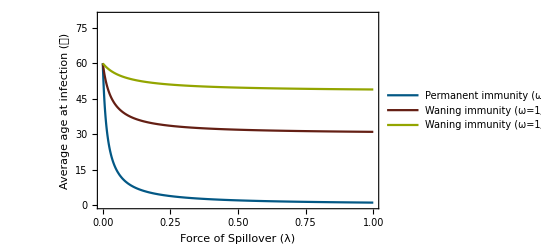

```mathematica
AbarFig=Plot[{(ABar/.Pars/.{ω->0}),(ABar/.Pars/.{ω->1/60}),(ABar/.Pars/.{ω->1/15})},{λ,0,1},PlotRange->{0,80},Frame->True,LabelStyle->Black,FrameLabel->{"Force of Spillover (λ)","Average age at infection (𝒜̄)"},BaseStyle->{FontSize->12,FontColor->Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},PlotStyle->{CMYKColor[0.98,0.48,0.21,0.34],CMYKColor[0.23,0.76,0.85,0.49],CMYKColor[0.24,0.15,1,0.24]},ImageSize->400,Epilog->Inset[MyLegend,{0.7,65}]]
```

```mathematica
Export[HomePath<>"\Figure1.png",AbarFig ,ImageResolution->600]
```

C:\Work\Current Projects\Porous Spillover Prevention\Figures\FigureAbar.png

## Solutions for ℬ with age-specific transition to disease -- lifelong immunity

Here we assume that the rate of transition from I to M is sufficiently small for the M class to be ignored (I ~ I-M). This requires that μ be small or v large.

```mathematica
ApproxAges=FullSimplify[ToRadicals[DSolve[{S'[a]==-λ S[a]-δ S[a],Ι'[a]==λ S[a]-γ Ι[a]-δ Ι[a],R'[a]==γ (Ι[a])-δ R[a],S[0]==b,Ι[0]==0,R[0]==0},{S[a],Ι[a],R[a]},a]]]
```

{{R[a]→-(b ⅇ^(-a δ) ((-1+ⅇ^(-a λ)) γ+λ-ⅇ^(-a γ) λ))/(γ-λ),S[a]→b ⅇ^(-a (δ+λ)),Ι[a]→-(b (ⅇ^(-a (γ+δ))-ⅇ^(-a (δ+λ))) λ)/(γ-λ)}}

The (small) number of new cases of disease per unit time is then given by:

```mathematica
ApproxDisease=1/(b/δ)FullSimplify[Integrate[μ[a] Ι[a],{a,0,∞}]/.ApproxAges]
```

{(δ ∫_0^∞ -(b (ⅇ^(-a (γ+δ))-ⅇ^(-a (δ+λ))) λ μ[a])/(γ-λ)ⅆa)/b}

Note that here the total population size is approximately b/δ because we have assumed the transition to clinical disease is sufficiently rare for the impact of virulence on population size to be ignored.

### Derive the conditions for the effect to occur when the rate of clinical disease increases linearly with age

Calculate the burden under the assumptions of linear increase in transition rate, μ

```mathematica
Linℬ=FullSimplify[ApproxDisease/.{μ[a]->μo+α a},Assumptions->{Re[γ+δ]>0&&Re[δ+λ]>0}]
```

{(δ λ (α (γ+2 δ+λ)+(γ+δ) (δ+λ) μo))/((γ+δ)^2 (δ+λ)^2)}

Calculate the slope of the burden with respect to the force of spillover

```mathematica
Slope=D[Linℬ,λ]
```

{(δ λ (α+(γ+δ) μo))/((γ+δ)^2 (δ+λ)^2)-(2 δ λ (α (γ+2 δ+λ)+(γ+δ) (δ+λ) μo))/((γ+δ)^2 (δ+λ)^3)+(δ (α (γ+2 δ+λ)+(γ+δ) (δ+λ) μo))/((γ+δ)^2 (δ+λ)^2)}

Find where the slope is zero

```mathematica
IsFlat=FullSimplify[Solve[Slope==0,λ]]
```

{{λ→-(δ (α (γ+2 δ)+δ (γ+δ) μo))/(-α γ+δ (γ+δ) μo)}}

Because λ must be positive, αγ > δ (γ+δ) μo

Find the curvature of burden with respect to the force of spillover:

```mathematica
Curve=D[Linℬ,{λ,2}]
```

{(δ λ (-(4 (α+(γ+δ) μo))/(δ+λ)^3+(6 (α (γ+2 δ+λ)+(γ+δ) (δ+λ) μo))/(δ+λ)^4))/(γ+δ)^2+(2 δ ((α+(γ+δ) μo)/(δ+λ)^2-(2 (α (γ+2 δ+λ)+(γ+δ) (δ+λ) μo))/(δ+λ)^3))/(γ+δ)^2}

And then its specific value where the slope is equal to zero:

```mathematica
CurveAtFlat=FullSimplify[Curve/.IsFlat]
```

{{-(α γ-δ (γ+δ) μo)^4/(8 α^3 δ^2 (γ+δ)^5)}}

Find the peak by identifying the conditions that force the curvature to be negative:

```mathematica
Reduce[CurveAtFlat<0&&α γ>δ (γ+δ) μo&&b>0&&α>0&&γ>0&&δ>0]
```

b>0&&δ>0&&γ>0&&α>0&&μo<(α γ)/(γ δ+δ^2)

Rearranging yields the text equation:

α > (μo δ(γ+δ))/γ

### Generate a figure showing the relationship between spillover pressure and burden

#### Set some basic parameters and definitions

```mathematica
Linℬ=(δ λ (α (γ+2 δ+λ)+(γ+δ) (δ+λ) μo))/((γ+δ)^2 (δ+λ)^2);
```

```mathematica
UpBound=0.002;
```

Note that discrepancies between the analytical and numerical results arise if the age classes are truncated too soon. We use a maximum age of 500 here to quantify accuracy of our approximation with respect to model parameters. Because including unrealistically old individuals in the calculations may bias our results, however, we use a lower and more realistic limit when we focus on the realized risk of negative health impacts in the Lassa virus system later on. Note that the age class limit has no impact on the qualitative results and influences only the specific values.

```mathematica
MaxAge=500;
```

```mathematica
Pars1={b->100,μo->1,α->0,γ->1/(14/365),δ->1/60,v->1};
```

```mathematica
Pars2={b->100,μo->1,α->δ(μo(5-1)),γ->1/(14/365),δ->1/60,v->1};
```

```mathematica
Pars3={b->100,μo->1,α->δ(μo(10-1)),γ->1/(14/365),δ->1/60,v->1};
```

#### And move along

```mathematica
MyLegend=LineLegend[{CMYKColor[0.98,0.48,0.21,0.34],CMYKColor[0.23,0.76,0.85,0.49],CMYKColor[0.24,0.15,1,0.24]},{"Age-indepdendent","5X increase","10X increase"}]
```

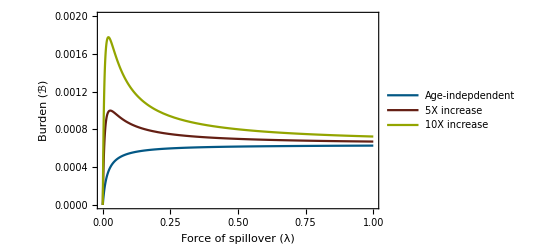

```mathematica
FigureBurden=Plot[{Linℬ//.Pars1,Linℬ//.Pars2,Linℬ//.Pars3},{λ,0,1},PlotRange->{0,UpBound},Frame->True,FrameLabel->{"Force of spillover (λ)","Burden (ℬ)"},BaseStyle->{FontSize->12,FontColor->Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},PlotStyle->{CMYKColor[0.98,0.48,0.21,0.34],CMYKColor[0.23,0.76,0.85,0.49],CMYKColor[0.24,0.15,1,0.24]},ImageSize->400,Epilog->Inset[MyLegend,{0.8,0.0015}]]
```

### Now check the approximation with exact numerics

```mathematica
Module[{i,j},Burden={};For[i=0,i<50,i++,ThisLambda=0+.02*i;MySols=NDSolve[{S'[a]==-λ S[a]-δ S[a],Ι'[a]==λ S[a]-γ Ι[a]-(μo+α a) Ι[a]-δ Ι[a],M'[a]==(μo+α a) Ι[a]-v M[a]-δ M[a]-γ M[a],R'[a]==γ(Ι[a]+M[a])-δ R[a],S[0]==b,Ι[0]==0,M[0]==0,R[0]==0}//.Pars1/.λ->ThisLambda,{S[a],Ι[a],M[a],R[a]},{a,MaxAge}];Ν=NIntegrate[(S[a]+Ι[a]+M[a]+R[a])/.MySols,{a,0,MaxAge}];ℬ=NIntegrate[(1/Ν(μo+α a) Ι[a]/.MySols/.TPS)//.Pars1/.λ->ThisLambda,{a,0,MaxAge},AccuracyGoal->8];Burden=Append[Burden,Flatten[ {ThisLambda,ℬ}]]]]
```

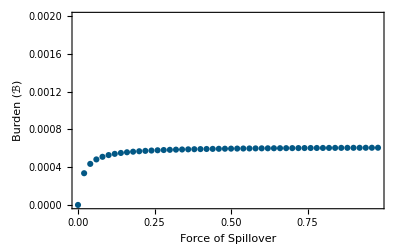

```mathematica
P1=ListPlot[Transpose[{Burden[[All,1]],Burden[[All,2]]}],PlotRange->{0,UpBound},Joined->False,Frame->True,FrameLabel->{"Force of Spillover","Burden (ℬ)"},BaseStyle->{FontSize->12,FontColor->Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},PlotStyle->{CMYKColor[0.98,0.48,0.21,0.34]}]
```

```mathematica
Module[{i,j},Burden={};For[i=0,i<50,i++,ThisLambda=0+.02*i;MySols=NDSolve[{S'[a]==-λ S[a]-δ S[a],Ι'[a]==λ S[a]-γ Ι[a]-(μo+α a) Ι[a]-δ Ι[a],M'[a]==(μo+α a) Ι[a]-v M[a]-δ M[a]-γ M[a],R'[a]==γ(Ι[a]+M[a])-δ R[a],S[0]==b,Ι[0]==0,M[0]==0,R[0]==0}//.Pars2/.λ->ThisLambda,{S[a],Ι[a],M[a],R[a]},{a,MaxAge}];Ν=NIntegrate[(S[a]+Ι[a]+M[a]+R[a])/.MySols,{a,0,MaxAge}];ℬ=NIntegrate[(1/Ν(μo+α a) Ι[a]/.MySols/.TPS)//.Pars2/.λ->ThisLambda,{a,0,MaxAge},AccuracyGoal->8];Burden=Append[Burden,Flatten[ {ThisLambda,ℬ}]]]]
```

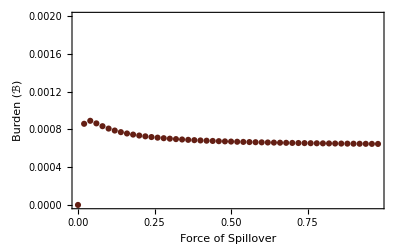

```mathematica
P2=ListPlot[Transpose[{Burden[[All,1]],Burden[[All,2]]}],PlotRange->{0,UpBound},Joined->False,Frame->True,FrameLabel->{"Force of Spillover","Burden (ℬ)"},BaseStyle->{FontSize->12,FontColor->Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},PlotStyle->{CMYKColor[0.23,0.76,0.85,0.49]}]
```

```mathematica
Module[{i,j},Burden={};For[i=0,i<50,i++,ThisLambda=0+.02*i;MySols=NDSolve[{S'[a]==-λ S[a]-δ S[a],Ι'[a]==λ S[a]-γ Ι[a]-(μo+α a) Ι[a]-δ Ι[a],M'[a]==(μo+α a) Ι[a]-v M[a]-δ M[a]-γ M[a],R'[a]==γ(Ι[a]+M[a])-δ R[a],S[0]==b,Ι[0]==0,M[0]==0,R[0]==0}//.Pars3/.λ->ThisLambda,{S[a],Ι[a],M[a],R[a]},{a,MaxAge}];Ν=NIntegrate[(S[a]+Ι[a]+M[a]+R[a])/.MySols,{a,0,MaxAge},AccuracyGoal->8];ℬ=NIntegrate[(1/Ν(μo+α a) Ι[a]/.MySols/.TPS)//.Pars3/.λ->ThisLambda,{a,0,MaxAge}];Burden=Append[Burden,Flatten[ {ThisLambda,ℬ}]]]]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

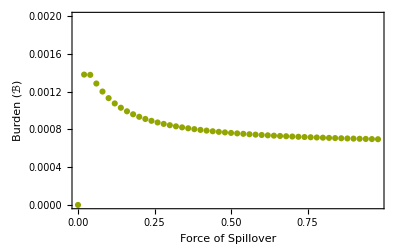

```mathematica
P3=ListPlot[Transpose[{Burden[[All,1]],Burden[[All,2]]}],PlotRange->{0,UpBound},Joined->False,Frame->True,FrameLabel->{"Force of Spillover","Burden (ℬ)"},BaseStyle->{FontSize->12,FontColor->Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},PlotStyle->{CMYKColor[0.24,0.15,1,0.24]}]
```

### Compare analytical approximation to exact numerical solutions

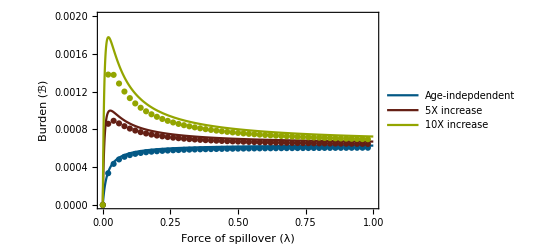

```mathematica
FigureBurden=Show[{FigureBurden,P1,P2,P3}]
```

```mathematica
Export[HomePath<>"\Figure2.png",FigureBurden ,ImageResolution->600]
```

C:\Work\Current Projects\Porous Spillover Prevention\Figures\Figure2.png

## Solutions for ℬ with age-specific transition to disease -- waning immunity

### Deriving an approximate result that assumes the M class is negligible

```mathematica
ApproxAges=FullSimplify[ToRadicals[DSolve[{S'[a]==-λ S[a]-δ S[a]+ω R[a],Ι'[a]==λ S[a]-γ Ι[a]-δ Ι[a],R'[a]==γ (Ι[a])-δ R[a]-ω R[a],S[0]==b,Ι[0]==0,R[0]==0},{S[a],Ι[a],R[a]},a]]];
```

Some simplifications for the paper text

```mathematica
SimpForAppendix=FullSimplify[(1/(2 √(γ^2+(λ-ω)^2-2 γ (λ+ω)) (λ ω+γ (λ+ω)))b ⅇ^(-1/2 a (γ+2 δ+λ+ω+√((γ-λ)^2-2 (γ+λ) ω+ω^2))) λ (-ω √(γ^2+(λ-ω)^2-2 γ (λ+ω))-ⅇ^(a √(γ^2+(λ-ω)^2-2 γ (λ+ω))) ω √(γ^2+(λ-ω)^2-2 γ (λ+ω))+2 ⅇ^(1/2 a (γ+λ+ω+√((γ-λ)^2-2 (γ+λ) ω+ω^2))) ω √(γ^2+(λ-ω)^2-2 γ (λ+ω))+(-1+ⅇ^(a √(γ^2+(λ-ω)^2-2 γ (λ+ω)))) ((λ-ω) ω+γ (2 λ+ω))))/.{γ^2+(λ-ω)^2-2 γ (λ+ω)->Subscript[k, 1],(γ-λ)^2-2 (γ+λ) ω+ω^2->Subscript[k, 2]},Assumptions->{λ>0,b>0,γ>0,ω>0}]
```

(b ⅇ^(-1/2 a (γ+2 δ+λ+ω+√k_2)) λ ((-1+ⅇ^(a √k_1)) ((λ-ω) ω+γ (2 λ+ω))-(1+ⅇ^(a √k_1)-2 ⅇ^(1/2 a (γ+λ+ω+√k_2))) ω √k_1))/(2 (λ ω+γ (λ+ω)) √k_1)

The (small) number of new cases of disease (per capita) per unit time is then given by:

```mathematica
ApproxDisease=1/(b/δ)FullSimplify[Integrate[μ[a] Ι[a],{a,0,∞}]/.ApproxAges]
```

{1/b δ ∫_0^∞ ((b ⅇ^(-1/2 a (γ+2 δ+λ+ω+√((γ-λ)^2-2 (γ+λ) ω+ω^2))) λ (-ω √(γ^2+(λ-ω)^2-2 γ (λ+ω))-ⅇ^(a √(γ^2+(λ-ω)^2-2 γ (λ+ω))) ω √(γ^2+(λ-ω)^2-2 γ (λ+ω))+2 ⅇ^(1/2 a (γ+λ+ω+√((γ-λ)^2-2 (γ+λ) ω+ω^2))) ω √(γ^2+(λ-ω)^2-2 γ (λ+ω))+(-1+ⅇ^(a √(γ^2+(λ-ω)^2-2 γ (λ+ω)))) ((λ-ω) ω+γ (2 λ+ω))) μ[a])/(2 √(γ^2+(λ-ω)^2-2 γ (λ+ω)) (λ ω+γ (λ+ω))))ⅆa}

Make the assumption that transition to clinical disease increases linearly with age:

```mathematica
Linℬ=FullSimplify[ApproxDisease/.{μ[a]->μo+α a},Assumptions->{Re[δ]>0&&Re[γ+2 δ+λ+ω-√(γ^2+(λ-ω)^2-2 γ (λ+ω))]>0}]
```

{(δ λ (δ μo (δ+ω) ((δ+λ) (δ+ω)+γ (δ+λ+ω))+α ((2 δ+λ) (δ+ω)^2+γ (δ^2+2 δ ω+ω (λ+ω)))))/(δ (δ+λ) (δ+ω)+γ δ (δ+λ+ω))^2}

Find the slope of the relationship between ℬ and λ

```mathematica
Slope=D[Linℬ,λ]
```

{(δ λ (δ μo (δ+ω) (γ+δ+ω)+α (γ ω+(δ+ω)^2)))/(δ (δ+λ) (δ+ω)+γ δ (δ+λ+ω))^2-(2 δ λ (γ δ+δ (δ+ω)) (δ μo (δ+ω) ((δ+λ) (δ+ω)+γ (δ+λ+ω))+α ((2 δ+λ) (δ+ω)^2+γ (δ^2+2 δ ω+ω (λ+ω)))))/(δ (δ+λ) (δ+ω)+γ δ (δ+λ+ω))^3+(δ (δ μo (δ+ω) ((δ+λ) (δ+ω)+γ (δ+λ+ω))+α ((2 δ+λ) (δ+ω)^2+γ (δ^2+2 δ ω+ω (λ+ω)))))/(δ (δ+λ) (δ+ω)+γ δ (δ+λ+ω))^2}

Locate peaks and valleys

```mathematica
IsFlat=FullSimplify[Solve[Slope==0,λ]]
```

{{λ→-((γ+δ) (α (γ+2 δ)+δ (γ+δ) μo) (δ+ω)^2)/(δ (γ+δ) μo (δ+ω) (γ+δ+ω)+α γ (-δ (γ+δ)+(γ+2 δ) ω+ω^2))}}

Look only for peaks and valleys associated with positive values of λ:

```mathematica
FullSimplify[Reduce[(λ/.IsFlat)>0&&ω>0&&δ>0&&γ>0&&α>0&&μo>0,α]]
```

α>(δ (γ+δ) μo (δ+ω) (γ+δ+ω))/(γ (δ (γ+δ)-(γ+2 δ) ω-ω^2))&&μo>0&&ω>0&&((ω<δ&&ω (γ+2 δ+ω)<δ (γ+δ)&&δ<ω+√2 ω)||(γ>0&&δ≥ω+√2 ω))

```mathematica
FullSimplify[Reduce[ω (γ+2 δ+ω)<δ (γ+δ)&&ω>0&&δ>0&&γ>0&&α>0&&μo>0,δ]]
```

ω>0&&γ>0&&α>0&&μo>0&&γ+2 δ>2 ω+√(γ^2+8 ω^2)

Necessary conditions for the effect to occur (an internal maxima) are that:

Cond1: α>(δ (γ+δ) μo (δ+ω) (γ+δ+ω))/(γ (δ (γ+δ)-(γ+2 δ) ω-ω^2))

And that Cond2a or both Cond2b and Cond2c hold

Cond2a:δ≥(1+√2) ω
or

Cond2b: ω<δ<(1+√2) ω

Cond2c: δ > ω+(√(γ^2+8 ω^2)-γ)/2

Check to see if we have identified a maxima:

```mathematica
Curve=D[Linℬ,{λ,2}]
```

{δ λ (-(4 (γ δ+δ (δ+ω)) (δ μo (δ+ω) (γ+δ+ω)+α (γ ω+(δ+ω)^2)))/(δ (δ+λ) (δ+ω)+γ δ (δ+λ+ω))^3+(6 (γ δ+δ (δ+ω))^2 (δ μo (δ+ω) ((δ+λ) (δ+ω)+γ (δ+λ+ω))+α ((2 δ+λ) (δ+ω)^2+γ (δ^2+2 δ ω+ω (λ+ω)))))/(δ (δ+λ) (δ+ω)+γ δ (δ+λ+ω))^4)+2 δ ((δ μo (δ+ω) (γ+δ+ω)+α (γ ω+(δ+ω)^2))/(δ (δ+λ) (δ+ω)+γ δ (δ+λ+ω))^2-(2 (γ δ+δ (δ+ω)) (δ μo (δ+ω) ((δ+λ) (δ+ω)+γ (δ+λ+ω))+α ((2 δ+λ) (δ+ω)^2+γ (δ^2+2 δ ω+ω (λ+ω)))))/(δ (δ+λ) (δ+ω)+γ δ (δ+λ+ω))^3)}

```mathematica
CurveAtFlat=FullSimplify[Curve/.IsFlat]
```

{{-((δ (γ+δ) μo (δ+ω) (γ+δ+ω)+α γ (-δ (γ+δ)+(γ+2 δ) ω+ω^2))^4)/(8 α^3 δ^4 (γ+δ)^3 (δ+ω)^2 (γ^2+(δ+ω)^2+γ (2 δ+ω))^3)}}

```mathematica
Reduce[CurveAtFlat>0&&ω>0γ>0]
```

False

Indeed, anytime we have a point of zero slope it is a maxima.

### Generate a figure showing the relationship between spillover pressure and burden

#### Set some basic parameters and load the approximation for burden

```mathematica
UpBound=0.007;
```

```mathematica
MaxAge=500;
```

```mathematica
Linℬ=(δ λ (δ μo (δ+ω) ((δ+λ) (δ+ω)+γ (δ+λ+ω))+α ((2 δ+λ) (δ+ω)^2+γ (δ^2+2 δ ω+ω (λ+ω)))))/(δ (δ+λ) (δ+ω)+γ δ (δ+λ+ω))^2;
```

```mathematica
Pars1={b->100,μo->1,α->δ(μo(5-1)),γ->1/(14/365),δ->1/60,ω->0,v->1};
```

```mathematica
Pars2={b->100,μo->1,α->δ(μo(5-1)),γ->1/(14/365),δ->1/60,ω->1/180,v->1};
```

```mathematica
Pars3={b->100,μo->1,α->δ(μo(5-1)),γ->1/(14/365),δ->1/60,ω->1/60,v->1};
```

#### Move on along

```mathematica
MyLegend=LineLegend[{CMYKColor[0.24,0.15,1,0.24],CMYKColor[0.23,0.76,0.85,0.49],CMYKColor[0.98,0.48,0.21,0.34]},{"ω = δ","ω = δ/3","ω = 0"}]
```

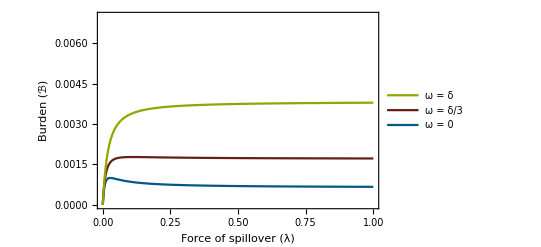

```mathematica
FigureWane=Plot[{Linℬ//.Pars1,Linℬ//.Pars2,Linℬ//.Pars3},{λ,0,1},PlotRange->{0,UpBound},Frame->True,FrameLabel->{"Force of spillover (λ)","Burden (ℬ)"},BaseStyle->{FontSize->12,FontColor->Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},PlotStyle->{CMYKColor[0.98,0.48,0.21,0.34],CMYKColor[0.23,0.76,0.85,0.49],CMYKColor[0.24,0.15,1,0.24]},ImageSize->400,Epilog->Inset[MyLegend,{0.83,0.0053}]]
```

### Now check the approximation with exact numerics

Here you must include the M class or you get a leak... It does not matter for the case of permanent immunity because, there, once they go to M they are out of the system. Here, however, M can get churned back into S via R.

```mathematica
Module[{i,j},Burden={};For[i=0,i<50,i++,ThisLambda=0+.02*i;MySols=NDSolve[{S'[a]==-λ S[a]-δ S[a]+ω R[a],Ι'[a]==λ S[a]-γ Ι[a]-(μo+α a) Ι[a]-δ Ι[a],M'[a]==(μo+α a) Ι[a]-γ M[a]-δ M[a]-v M[a],R'[a]==γ (M[a]+Ι[a])-ω R[a]-δ R[a],S[0]==b,Ι[0]==0,M[0]==0,R[0]==0}//.Pars1/.λ->ThisLambda,{S[a],Ι[a],M[a],R[a]},{a,MaxAge}];
Ν=NIntegrate[(S[a]+Ι[a]+M[a]+R[a])/.MySols,{a,0,MaxAge}];ℬ=NIntegrate[(1/Ν(μo+α a) Ι[a]/.MySols)//.Pars1/.λ->ThisLambda,{a,0,MaxAge},AccuracyGoal->8];Burden=Append[Burden,Flatten[ {ThisLambda,ℬ}]]]]
```

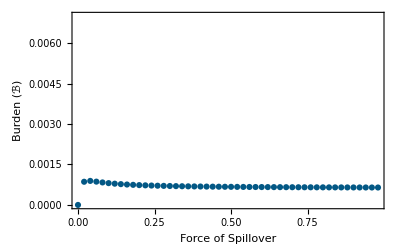

```mathematica
P1=ListPlot[Transpose[{Burden[[All,1]],Burden[[All,2]]}],PlotRange->{0,UpBound},Joined->False,Frame->True,FrameLabel->{"Force of Spillover","Burden (ℬ)"},BaseStyle->{FontSize->12,FontColor->Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},PlotStyle->{CMYKColor[0.98,0.48,0.21,0.34]}]
```

```mathematica
Module[{i,j},Burden={};For[i=0,i<50,i++,ThisLambda=0+.02*i;MySols=NDSolve[{S'[a]==-λ S[a]-δ S[a]+ω R[a],Ι'[a]==λ S[a]-γ Ι[a]-(μo+α a) Ι[a]-δ Ι[a],M'[a]==(μo+α a) Ι[a]-γ M[a]-δ M[a]-v M[a],R'[a]==γ (M[a]+Ι[a])-ω R[a]-δ R[a],S[0]==b,Ι[0]==0,M[0]==0,R[0]==0}//.Pars2/.λ->ThisLambda,{S[a],Ι[a],M[a],R[a]},{a,MaxAge}];
Ν=NIntegrate[(S[a]+Ι[a]+M[a]+R[a])/.MySols,{a,0,MaxAge}];ℬ=NIntegrate[(1/Ν(μo+α a) Ι[a]/.MySols)//.Pars2/.λ->ThisLambda,{a,0,MaxAge},AccuracyGoal->8];Burden=Append[Burden,Flatten[ {ThisLambda,ℬ}]]]]
```

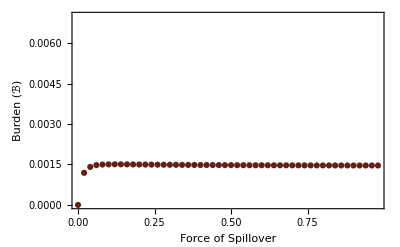

```mathematica
P2=ListPlot[Transpose[{Burden[[All,1]],Burden[[All,2]]}],PlotRange->{0,UpBound},Joined->False,Frame->True,FrameLabel->{"Force of Spillover","Burden (ℬ)"},BaseStyle->{FontSize->12,FontColor->Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},PlotStyle->{CMYKColor[0.23,0.76,0.85,0.49]}]
```

```mathematica
Module[{i,j},Burden={};For[i=0,i<50,i++,ThisLambda=0+.02*i;MySols=NDSolve[{S'[a]==-λ S[a]-δ S[a]+ω R[a],Ι'[a]==λ S[a]-γ Ι[a]-(μo+α a) Ι[a]-δ Ι[a],M'[a]==(μo+α a) Ι[a]-γ M[a]-δ M[a]-v M[a],R'[a]==γ (M[a]+Ι[a])-ω R[a]-δ R[a],S[0]==b,Ι[0]==0,M[0]==0,R[0]==0}//.Pars3/.λ->ThisLambda,{S[a],Ι[a],M[a],R[a]},{a,MaxAge}];
Ν=NIntegrate[(S[a]+Ι[a]+M[a]+R[a])/.MySols,{a,0,MaxAge}];ℬ=NIntegrate[(1/Ν(μo+α a) Ι[a]/.MySols)//.Pars3/.λ->ThisLambda,{a,0,MaxAge},AccuracyGoal->8];Burden=Append[Burden,Flatten[ {ThisLambda,ℬ}]]]]
```

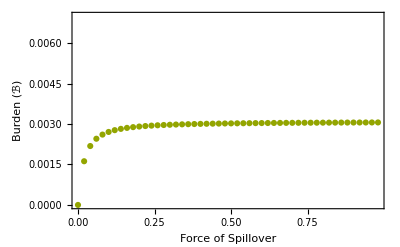

```mathematica
P3=ListPlot[Transpose[{Burden[[All,1]],Burden[[All,2]]}],PlotRange->{0,UpBound},Joined->False,Frame->True,FrameLabel->{"Force of Spillover","Burden (ℬ)"},BaseStyle->{FontSize->12,FontColor->Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},PlotStyle->{CMYKColor[0.24,0.15,1,0.24]}]
```

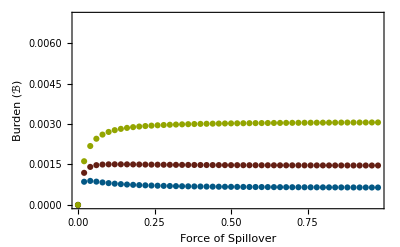

```mathematica
FigureWaneExact=Show[{P1,P2,P3}]
```

### Compile and Compare

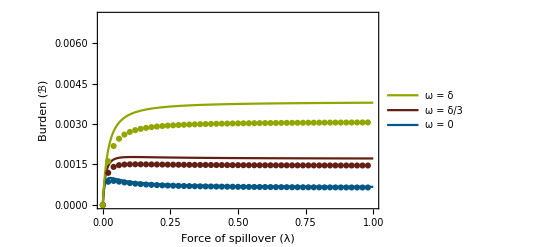

```mathematica
WaneImpact=Show[{FigureWane,FigureWaneExact}]
```

```mathematica
Export[HomePath<>"\Figure3.png",WaneImpact ,ImageResolution->600]
```

C:\Work\Current Projects\Porous Spillover Prevention\Figures\Figure3.png

### Why does this approximation do worse?

I am currently speculating that the approximation does worse simply because with waning immunity the number of individuals moving into the M class (burden) is greater. In other words, the number of individuals in the M class -- that our approximation ignores -- rises with waning immunity. This checks out at equilibrium (see start of notebook).

## Analyses of Lassa Data

Completed September 22, 2023

Revised to use exact formula November 22, 2023

## Estimates for age-independent values of model parameters

As described in the main text, we use values reported in the literature to set estimates for model parameters. Because the extent to which seroreversion occurs is debated, we consider two cases: one where immunity wanes over time and one where it is permanent. Replacements for parameters corresponding to these two cases follow:

```mathematica
LassaParsWaning={b->24.75,v->5.22,ω->0.064,γ->12.17,μ->3.05,δ->0.0165};
```

```mathematica
LassaParsWaneless={b->24.75,v->5.22,ω->0.0,γ->12.17,μ->3.05,δ->0.0165};
```

In the above, birth rate has been set to yield a local population size of 1500

```mathematica
(b/δ)/.LassaParsWaning
```

1500.

These values were derived from the literature as follows:

#### Disease independent mortality, δ

We used data from the WorldBank reporting country specific mortality for the set of countries for which we had serosurveys available to estimate an average lifespan within West Africa of 60.48. Although this varies somewhat across countries, we use a single representative value to simplify results; using precise values for individual countries has little impact on results.

Ghana 63.8
Guinea 58.9
Liberia 60.7
Mali 58.9
Sierra Leone 60.1

```mathematica
Mean[{63.8,58.9,60.7,58.9,60.1}]
```

60.48

#### Rate of recovery from Lassa virus infection, γ

The literature suggests individuals develop symptoms betweeen 7 and 21 days after exposure (https://doi.org/10.1038/s41579-022-00789-8) and clear the infection 17 days following symptom onset, on average (10.1136/bmj.327.7426.1271). Based on these numbers we take 30 days as a reasonable estimate for the time required for an individual to clear an infection and develop antibodies.

#### Disease dependent mortality, v

The literature suggests that 30% of individuals with symptomatic infections ultimately die (https://doi.org/10.1038/s41579-022-00789-8). We set the disease dependent mortality rate equal to 5.22 recognizing that v=(0.3(γ+δ))/0.7.

```mathematica
SetVir={v->(CFR (γ+δ))/(1-CFR)}/.{γ->365/30,δ->1/(60.48),CFR->0.3}
```

{v→5.22137}

#### Rate of advance to symptomatic infection, μ

The literature suggests that 20% of LASV infections result in symptoms (https://doi.org/10.1038/s41579-022-00789-8). We set the rate of advance to a symptomatic state to 3.05 recognizing that μ=(0.2(γ+δ))/0.8.

```mathematica
{μ->(m (γ+δ))/(1-m)}/.{γ->365/30,δ->1/(60.48),m->0.2}
```

{μ→3.0458}

## Estimating the relationship between age and disease severity

The scope for unintended consequences depends on the relationship between disease severity and age at infection. Our model assumes that the relationship between age and disease manifests through the rate at which an infected individual develops symptomatic disease, μ. Unfortunately, data on this specific relationship is not available and is unlikely to ever be so because it would require systematic tracking of individuals of different ages who become infected prior to development of symptoms. Data is available, however, on the rate at which symptomatic individuals admitted to the hospital ultimately die as a function of their age (Illori et al. 2019). Thus, we use this as a surrogate measure to parameterize our linear function relating the rate of transition to symptomatic disease to age:

```mathematica
μ[a]->μo+α a
```

μ[a]→a α+μo

Data presented in Illori et al. (2019) allows us to estimate these parameters using data presented in their Table 2 which reports case-fatality rate (%) as a function of age class. Their data follows using the mid-point of their age classes:

```mathematica
Clear[δ]
```

```mathematica
RawIlloriData={{5,0.111},{15,0.212},{25,0.205},{35,0.256},{45,0.323},{55,0.32},{65,0.382}};
```

We transform this data to rates:

```mathematica
RateIlloriData=Table[{RawIlloriData[[i,1]],(RawIlloriData[[i,2]] (γ+δ))/(1-RawIlloriData[[i,2]])/.LassaParsWaneless},{i,1,Length[RawIlloriData]}]
```

{{5,1.5216},{15,3.2786},{25,3.14243},{35,4.1932},{45,5.81424},{55,5.73482},{65,7.53276}}

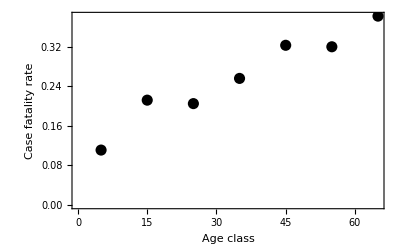

```mathematica
RawDatPlot=ListPlot[RawIlloriData,PlotStyle->{Black,PointSize->.02},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Age class","Case fatality rate"},BaseStyle->{FontSize->14}]
```

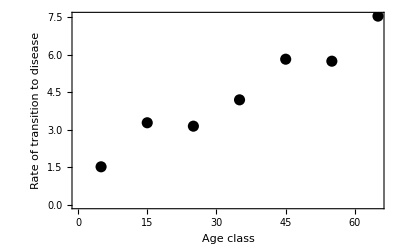

```mathematica
RateDatPlot=ListPlot[RateIlloriData,PlotStyle->{Black,PointSize->.02},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Age class","Rate of transition to disease"},BaseStyle->{FontSize->14}]
```

```mathematica
RealFit=Fit[RateIlloriData,{1,x},x]
```

1.25745+0.0914919 x

This results in the following estimates for intercept and slope:

```mathematica
IlloriFit={μo->1.26,α->.091};
```

Generate an alternative scenario where the slope is 50% greater than we estimate:

```mathematica
IlloriFitPlus50={μo->1.26,α->.091+0.5*.091}
```

{μo→1.26,α→0.1365}

Generate an alternative scenario where the slope is 100% greater than we estimate:

```mathematica
IlloriFitPlus100={μo->1.26,α->.091+1.0*.091}
```

{μo→1.26,α→0.182}

```mathematica
RawFit=Fit[RawIlloriData,{1,x},x]
```

0.115054+0.00409643 x

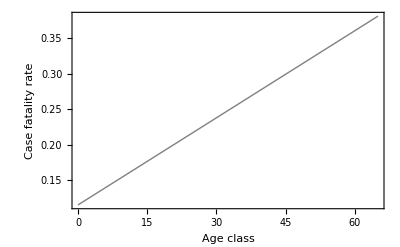

```mathematica
RawFitPlot=Plot[RawFit,{x,0,65},PlotStyle->{Thick,Gray},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Age class","Case fatality rate"},BaseStyle->{FontSize->14}]
```

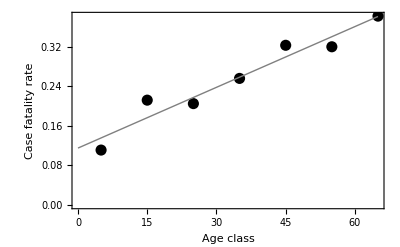

```mathematica
IlloriPlot=Show[{RawDatPlot,RawFitPlot}]
```

```mathematica
Export["C:\\Pandemic Laptop Work\\Current Projects\\Porous Spillover Prevention\\Figures\\FigureA1.png",IlloriPlot,ImageResolution->400]
```

C:\Pandemic Laptop Work\Current Projects\Porous Spillover Prevention\Figures\FigureA1.png

## Testing if unanticipated consequences can occur using the exact expressions

Here we use a maximum age of 100 because we wish to develop more detailed and realistic predictions for a real-world scenario.

```mathematica
MaxAge=100;
```

### Lifelong Immunity

This module uses numerical solutions to the ordinary differential equations to calculate the steady state age distribution of infected individuals and numerical integration to subsequently calculate burden. This is done for 50 different values of force of spillover. This first module uses the relationship between age and rate of transition to the diseased state estimated from the data.

```mathematica
Module[{i,j},Burden={};For[i=0,i<50,i++,ThisLambda=0+.012*i;MySols=NDSolve[{S'[a]==-λ S[a]-δ S[a],Ι'[a]==λ S[a]-γ Ι[a]-(μo+α a) Ι[a]-δ Ι[a],M'[a]==(μo+α a) Ι[a]-v M[a]-δ M[a]-γ M[a],R'[a]==γ(Ι[a]+M[a])-δ R[a],S[0]==b,Ι[0]==0,M[0]==0,R[0]==0}//.LassaParsWaneless/.IlloriFit/.λ->ThisLambda,{S[a],Ι[a],M[a],R[a]},{a,MaxAge}];Ν=NIntegrate[(S[a]+Ι[a]+M[a]+R[a])/.MySols,{a,0,MaxAge}];ℬ=NIntegrate[(1/Ν(μo+α a) Ι[a]/.MySols)//.LassaParsWaneless/.IlloriFit/.λ->ThisLambda,{a,0,MaxAge},AccuracyGoal->8];Burden=Append[Burden,Flatten[ {ThisLambda,ℬ}]]]]
```

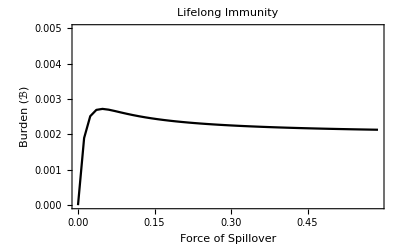

```mathematica
NoWaneBurdenPlot=ListPlot[Transpose[{Burden[[All,1]],Burden[[All,2]]}],PlotRange->{0,0.005},Joined->True,Frame->True,PlotLabel->"Lifelong Immunity",FrameLabel->{"Force of Spillover","Burden (ℬ)"},BaseStyle->{FontSize->12,FontColor->Black},LabelStyle->Black,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},PlotStyle->Black,ImageSize->400]
```

Do the same, but for a hypothetical case where rate of transition to disease increases 50% more rapidly with age than our estimate:

```mathematica
Module[{i,j},Burden={};For[i=0,i<50,i++,ThisLambda=0+.012*i;MySols=NDSolve[{S'[a]==-λ S[a]-δ S[a],Ι'[a]==λ S[a]-γ Ι[a]-(μo+α a) Ι[a]-δ Ι[a],M'[a]==(μo+α a) Ι[a]-v M[a]-δ M[a]-γ M[a],R'[a]==γ(Ι[a]+M[a])-δ R[a],S[0]==b,Ι[0]==0,M[0]==0,R[0]==0}//.LassaParsWaneless/.IlloriFitPlus50/.λ->ThisLambda,{S[a],Ι[a],M[a],R[a]},{a,MaxAge}];Ν=NIntegrate[(S[a]+Ι[a]+M[a]+R[a])/.MySols,{a,0,MaxAge},AccuracyGoal->8];ℬ=NIntegrate[(1/Ν(μo+α a) Ι[a]/.MySols)//.LassaParsWaneless/.IlloriFitPlus50/.λ->ThisLambda,{a,0,MaxAge}];Burden=Append[Burden,Flatten[ {ThisLambda,ℬ}]]]]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

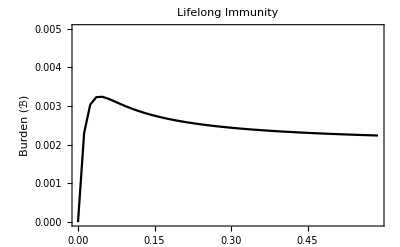

```mathematica
NoWaneBurdenPlotPlus50=ListPlot[Transpose[{Burden[[All,1]],Burden[[All,2]]}],PlotRange->{0,0.005},Joined->True,Frame->True,PlotLabel->"Lifelong Immunity",FrameLabel->{"","Burden (ℬ)"},BaseStyle->{FontSize->12,FontColor->Black},LabelStyle->Black,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},PlotStyle->Black,ImageSize->400]
```

Do the same, but for a hypothetical case where rate of transition to disease increases 100% more rapidly with age than our estimate:

```mathematica
Module[{i,j},Burden={};For[i=0,i<50,i++,ThisLambda=0+.012*i;MySols=NDSolve[{S'[a]==-λ S[a]-δ S[a],Ι'[a]==λ S[a]-γ Ι[a]-(μo+α a) Ι[a]-δ Ι[a],M'[a]==(μo+α a) Ι[a]-v M[a]-δ M[a]-γ M[a],R'[a]==γ(Ι[a]+M[a])-δ R[a],S[0]==b,Ι[0]==0,M[0]==0,R[0]==0}//.LassaParsWaneless/.IlloriFitPlus100/.λ->ThisLambda,{S[a],Ι[a],M[a],R[a]},{a,MaxAge}];Ν=NIntegrate[(S[a]+Ι[a]+M[a]+R[a])/.MySols,{a,0,MaxAge},AccuracyGoal->8];ℬ=NIntegrate[(1/Ν(μo+α a) Ι[a]/.MySols)//.LassaParsWaneless/.IlloriFitPlus100/.λ->ThisLambda,{a,0,MaxAge},AccuracyGoal->8];Burden=Append[Burden,Flatten[ {ThisLambda,ℬ}]]]]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

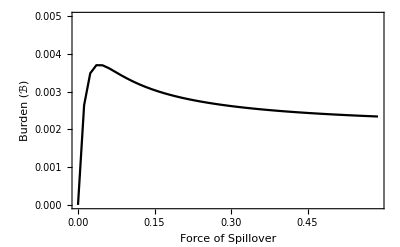

```mathematica
NoWaneBurdenPlotPlus100=ListPlot[Transpose[{Burden[[All,1]],Burden[[All,2]]}],PlotRange->{0,0.005},Joined->True,Frame->True,FrameLabel->{"Force of Spillover","Burden (ℬ)"},BaseStyle->{FontSize->12,FontColor->Black},PlotLabel->"",FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},PlotStyle->Black,ImageSize->400]
```

### Waning Immunity

This module uses numerical solutions to the ordinary differential equations to calculate the steady state age distribution of infected individuals and numerical integration to subsequently calculate burden. This is done for 50 different values of force of spillover. This first module uses the relationship between age and rate of transition to the diseased state estimated from the data. Subsequent modules explore sensitivity to increases in the slope of the relationship between age and transition to the diseased state.

```mathematica
Module[{i,j},Burden={};For[i=0,i<50,i++,ThisLambda=0+.012*i;MySols=NDSolve[{S'[a]==-λ S[a]-δ S[a]+ω R[a],Ι'[a]==λ S[a]-γ Ι[a]-(μo+α a) Ι[a]-δ Ι[a],M'[a]==(μo+α a) Ι[a]-γ M[a]-δ M[a]-v M[a],R'[a]==γ (M[a]+Ι[a])-ω R[a]-δ R[a],S[0]==b,Ι[0]==0,M[0]==0,R[0]==0}//.LassaParsWaning/.IlloriFit/.λ->ThisLambda,{S[a],Ι[a],M[a],R[a]},{a,MaxAge}];
Ν=NIntegrate[(S[a]+Ι[a]+M[a]+R[a])/.MySols,{a,0,MaxAge}];ℬ=NIntegrate[(1/Ν(μo+α a) Ι[a]/.MySols)//.LassaParsWaning/.IlloriFit/.λ->ThisLambda,{a,0,MaxAge},AccuracyGoal->8];Burden=Append[Burden,Flatten[ {ThisLambda,ℬ}]]]]
```

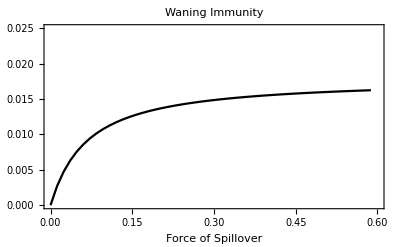

```mathematica
WaneBurdenPlot=ListPlot[Transpose[{Burden[[All,1]],Burden[[All,2]]}],PlotRange->{{0,0.6},{0,0.025}},Joined->True,Frame->True,PlotLabel->"Waning Immunity",FrameLabel->{"Force of Spillover",""},BaseStyle->{FontSize->12,FontColor->Black},LabelStyle->Black,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},PlotStyle->Black,ImageSize->400]
```

```mathematica
Module[{i,j},Burden={};For[i=0,i<50,i++,ThisLambda=0+.012*i;MySols=NDSolve[{S'[a]==-λ S[a]-δ S[a]+ω R[a],Ι'[a]==λ S[a]-γ Ι[a]-(μo+α a) Ι[a]-δ Ι[a],M'[a]==(μo+α a) Ι[a]-γ M[a]-δ M[a]-v M[a],R'[a]==γ (M[a]+Ι[a])-ω R[a]-δ R[a],S[0]==b,Ι[0]==0,M[0]==0,R[0]==0}//.LassaParsWaning/.IlloriFitPlus50/.λ->ThisLambda,{S[a],Ι[a],M[a],R[a]},{a,MaxAge}];
Ν=NIntegrate[(S[a]+Ι[a]+M[a]+R[a])/.MySols,{a,0,MaxAge}];ℬ=NIntegrate[(1/Ν(μo+α a) Ι[a]/.MySols)//.LassaParsWaning/.IlloriFitPlus50/.λ->ThisLambda,{a,0,MaxAge},AccuracyGoal->8];Burden=Append[Burden,Flatten[ {ThisLambda,ℬ}]]]]
```

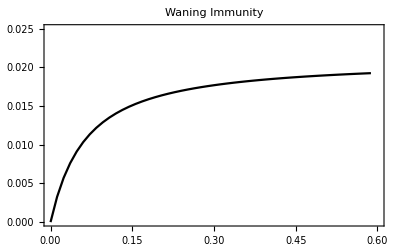

```mathematica
WaneBurdenPlotPlus50=ListPlot[Transpose[{Burden[[All,1]],Burden[[All,2]]}],PlotRange->{{0,0.6},{0,0.025}},Joined->True,Frame->True,PlotLabel->"Waning Immunity",FrameLabel->{"",""},BaseStyle->{FontSize->12,FontColor->Black},LabelStyle->Black,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},PlotStyle->Black,ImageSize->400]
```

```mathematica
Module[{i,j},Burden={};For[i=0,i<50,i++,ThisLambda=0+.012*i;MySols=NDSolve[{S'[a]==-λ S[a]-δ S[a]+ω R[a],Ι'[a]==λ S[a]-γ Ι[a]-(μo+α a) Ι[a]-δ Ι[a],M'[a]==(μo+α a) Ι[a]-γ M[a]-δ M[a]-v M[a],R'[a]==γ (M[a]+Ι[a])-ω R[a]-δ R[a],S[0]==b,Ι[0]==0,M[0]==0,R[0]==0}//.LassaParsWaning/.IlloriFitPlus100/.λ->ThisLambda,{S[a],Ι[a],M[a],R[a]},{a,MaxAge}];
Ν=NIntegrate[(S[a]+Ι[a]+M[a]+R[a])/.MySols,{a,0,MaxAge}];ℬ=NIntegrate[(1/Ν(μo+α a) Ι[a]/.MySols)//.LassaParsWaning/.IlloriFitPlus100/.λ->ThisLambda,{a,0,MaxAge},AccuracyGoal->8];Burden=Append[Burden,Flatten[ {ThisLambda,ℬ}]]]]
```

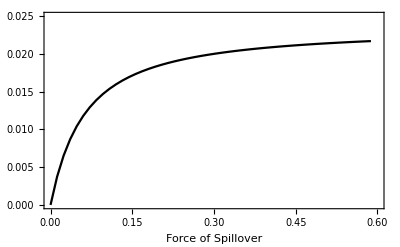

```mathematica
WaneBurdenPlotPlus100=ListPlot[Transpose[{Burden[[All,1]],Burden[[All,2]]}],PlotRange->{{0,0.6},{0,0.025}},Joined->True,Frame->True,FrameLabel->{"Force of Spillover",""},PlotLabel->"",BaseStyle->{FontSize->12,FontColor->Black},LabelStyle->Black,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},PlotStyle->Black,ImageSize->400]
```

## Identifying sites where unanticipated consequences are predicted to be possible

### Estimate force of spillover for sites with systematic serosurvey data available

#### The force of spillover can be estimated from seroprevalence data at steady state

```mathematica
SeroP=FullSimplify[R/(S+Ι+M+R)/.SimpEq]
```

{(γ λ (v+γ+δ+μ))/((γ+δ+μ) ((δ+λ) (δ+ω)+γ (δ+λ+ω))+v ((δ+λ+μ) (δ+ω)+γ (δ+λ+ω)))}

```mathematica
Force=FullSimplify[Solve[SeroP==ℛ,λ]]
```

{}

#### Compile Data and Estimate λ for each site

The human seroprevalence data comes from Basinski et al. 2021. Here it is loaded from the file “Prepped_Human _Seroprevalence _Data.csv”

```mathematica
SeroData=Import["C:\\Work\\Current Projects\\Porous Spillover Prevention\\Spillover Data\\Prepped_Human_Seroprevalence_Data.csv"];
```

```mathematica
SeroData[[1,All]]
```

{Longitude,Latitude,Country,Village,Species,NumPosVirus,NumTestVirus,PropVirus,Virus_Diagnostic_Method,NumPosAb,NumTestAb,PropAb,Ab_Diagnostic_Method,Antibody_Target,Source,Human_Random_Survey,Year,Bibtex,Survey_Dates,Survey_Date_Notes,TotPos,TotTest,genbank,uID,ArenaStat}

```mathematica
ℛ=SeroData[[All,12]]
```

{PropAb,0.153846,0.0243902,0.111111,0.266667,0.0410959,0.151515,0,0.333333,0.0909091,0.0434783,0.313725,0.05,0.137931,0.0540541,0,0,0.0384615,0.1,0.188679,0.0571429,0.416667,0.0392157,0.0625,0.08,0.0212766,0.137255,0.25,0.08,0.0612245,0.153846,0.425532,0.253846,0.417582,0.327869,0.54902,0.285714,0.405172,0.373494,0.340206,0.3,0.345029,0.256881,0.186441,0.331579,0.18,0.304348,0.251366,0.258333,0.0606061,0.0720721,0.0544218,0.0344828,0.077381,0.05,0.0490196,0.0375,0.18,0.476923,0.144068,0.102273,0.100486,0.10828,0.369714,0.150519,0.129825,0.152381,0.189767,0.198347,0.520737,0.310945,0.379032,0.0825688,0.0571429,0,0.0285714,0.0285714,0,0.16129,0.149254,0.0285714,0.0289855,0.1,0.44,0.145,0.41,0.0813743,0.00943396,0.0427553,0.0306122,0.141176,0.0507246,0.0425532,0,0.0776699}

Define some theoretical seroprevalences to see just how high the force of spillover would need to be to place a population in the danger zone for unanticipated consequences of spillover reduction:

```mathematica
Theoreticalℛ={0.65,0.75,0.85};
```

Calculate the force of spillover for each of the real populations assuming immunity wanes

```mathematica
ForceWane=Table[-(ℛ[[i]] (v+γ+δ) (γ+δ+μ) (δ+ω))/((v+γ+δ+μ) ((-1+ℛ[[i]]) γ+ℛ[[i]] (δ+ω)))/.LassaParsWaning,{i,2,Length[ℛ]}]
```

{0.015611,0.00214428,0.0107285,0.0312596,0.00367635,0.0153319,0,0.0430209,0.0085814,0.00389923,0.0393222,0.00451511,0.0137357,0.00490226,0,0,0.0034312,0.00953559,0.0199743,0.00519949,0.0615459,0.00350124,0.00571967,0.00746144,0.00186456,0.0136576,0.0286489,0.00746144,0.00559528,0.015611,0.0638366,0.0292409,0.0617793,0.0419682,0.105248,0.0343939,0.0586787,0.0513269,0.0443699,0.0368576,0.0453336,0.0297124,0.0196825,0.042681,0.0188521,0.0376277,0.0288585,0.0299395,0.00553509,0.00666418,0.00493755,0.00306348,0.00719653,0.00451511,0.00442198,0.00334205,0.0188521,0.0786648,0.0144505,0.00977718,0.00958717,0.0104217,0.0504994,0.0152131,0.0128071,0.0154354,0.0201167,0.0212531,0.093853,0.038815,0.0525575,0.00772275,0.00519949,0,0.00252276,0.00252276,0,0.0165128,0.0150626,0.00252276,0.00256042,0.00953559,0.0677327,0.01456,0.0598692,0.00760106,0.000816787,0.00383148,0.00270869,0.0141124,0.00458407,0.00381255,0,0.00722568}

Calculate the force of spillover for each of the theoretical populations assuming immunity wanes

```mathematica
TheoreticalForceWane=Table[-(Theoreticalℛ[[i]] (v+γ+δ) (γ+δ+μ) (δ+ω))/((v+γ+δ+μ) ((-1+Theoreticalℛ[[i]]) γ+Theoreticalℛ[[i]] (δ+ω)))/.LassaParsWaning,{i,1,Length[Theoreticalℛ]}]
```

{0.161244,0.26248,0.504882}

Calculate the force of spillover for each of the real populations assuming is permanent

```mathematica
ForceNoWane=Table[-(ℛ[[i]] (v+γ+δ) (γ+δ+μ) (δ+ω))/((v+γ+δ+μ) ((-1+ℛ[[i]]) γ+ℛ[[i]] (δ+ω)))/.LassaParsWaneless,{i,2,Length[ℛ]}]
```

{0.00319671,0.000439454,0.00219757,0.00639499,0.000753368,0.00313961,0,0.00879474,0.00175799,0.000799029,0.00804044,0.000925201,0.00281302,0.00100451,0,0,0.000703141,0.00195336,0.0040891,0.00106539,0.0125676,0.000717491,0.00117194,0.00152866,0.000382132,0.00279703,0.00586184,0.00152866,0.00114646,0.00319671,0.0130335,0.00598276,0.012615,0.0085801,0.0214342,0.00703484,0.0119842,0.0104874,0.00906977,0.00753762,0.00926623,0.00607904,0.00402944,0.00872545,0.00385964,0.00769475,0.00590464,0.00612542,0.00113414,0.00136539,0.00101174,0.000627801,0.00147442,0.000925201,0.000906123,0.000684876,0.00385964,0.0160464,0.00295928,0.00200282,0.00196392,0.00213477,0.0103189,0.00311531,0.00262299,0.00316078,0.00411821,0.00435055,0.0191269,0.00793697,0.010738,0.00158217,0.00106539,0,0.000517008,0.000517008,0,0.00338118,0.00308452,0.000517008,0.000524725,0.00195336,0.0138257,0.00298168,0.0122264,0.00155725,0.000167408,0.00078515,0.000555105,0.00289011,0.000939327,0.000781272,0,0.00148038}

Calculate the force of spillover for each of the theoretical populations assuming is permanent

```mathematica
TheoreticalForceNoWane=Table[-(Theoreticalℛ[[i]] (v+γ+δ) (γ+δ+μ) (δ+ω))/((v+γ+δ+μ) ((-1+Theoreticalℛ[[i]]) γ+Theoreticalℛ[[i]] (δ+ω)))/.LassaParsWaneless,{i,1,Length[Theoreticalℛ]}]
```

{0.0327265,0.0529481,0.100377}

### Now, calculate the predicted burden of spillover for each site

Again, here we use a maximum age of 100 for biological realism

```mathematica
MaxAge=100;
```

#### Lifelong Immunity with α estimated from the Illori et al. (2019) data.

```mathematica
Module[{i,j},Burden={};For[i=1,i≤Length[ForceNoWane],i++,ThisLambda=ForceNoWane[[i]];MySols=NDSolve[{S'[a]==-λ S[a]-δ S[a],Ι'[a]==λ S[a]-γ Ι[a]-(μo+α a) Ι[a]-δ Ι[a],M'[a]==(μo+α a) Ι[a]-v M[a]-δ M[a]-γ M[a],R'[a]==γ(Ι[a]+M[a])-δ R[a],S[0]==b,Ι[0]==0,M[0]==0,R[0]==0}//.LassaParsWaneless/.IlloriFit/.λ->ThisLambda,{S[a],Ι[a],M[a],R[a]},{a,MaxAge}];Ν=NIntegrate[(S[a]+Ι[a]+M[a]+R[a])/.MySols,{a,0,MaxAge},AccuracyGoal->8];ℬ=NIntegrate[(1/Ν(μo+α a) Ι[a]/.MySols)//.LassaParsWaneless/.IlloriFit/.λ->ThisLambda,{a,0,MaxAge},AccuracyGoal->8];Burden=Append[Burden,Flatten[ {ThisLambda,ℬ}]]]]
```

```mathematica
Module[{i,j},TheoBurden={};For[i=1,i≤Length[TheoreticalForceNoWane],i++,ThisLambda=TheoreticalForceNoWane[[i]];MySols=NDSolve[{S'[a]==-λ S[a]-δ S[a],Ι'[a]==λ S[a]-γ Ι[a]-(μo+α a) Ι[a]-δ Ι[a],M'[a]==(μo+α a) Ι[a]-v M[a]-δ M[a]-γ M[a],R'[a]==γ(Ι[a]+M[a])-δ R[a],S[0]==b,Ι[0]==0,M[0]==0,R[0]==0}//.LassaParsWaneless/.IlloriFit/.λ->ThisLambda,{S[a],Ι[a],M[a],R[a]},{a,MaxAge}];Ν=NIntegrate[(S[a]+Ι[a]+M[a]+R[a])/.MySols,{a,0,MaxAge},AccuracyGoal->8];ℬ=NIntegrate[(1/Ν(μo+α a) Ι[a]/.MySols)//.LassaParsWaneless/.IlloriFit/.λ->ThisLambda,{a,0,MaxAge}];TheoBurden=Append[TheoBurden,Flatten[ {ThisLambda,ℬ}]]]]
```

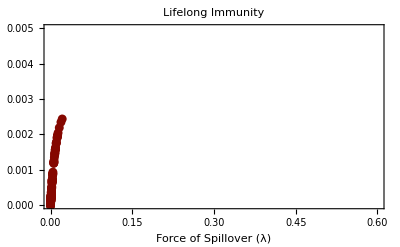

```mathematica
RealizedBurdenPlotWaneless=ListPlot[Burden,PlotRange->{{0,0.6},{0,0.005}},PlotLabel->"Lifelong Immunity",LabelStyle->Black,PlotStyle->{CMYKColor[0.07,0.95,1,0.44],PointSize->.016},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Force of Spillover (λ)",""},BaseStyle->{FontSize->14},ImageSize->400]
```

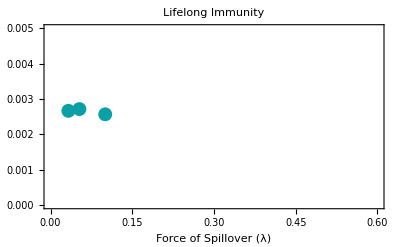

```mathematica
RealizedTheoBurdenPlotWaneless=ListPlot[TheoBurden,PlotRange->{{0,0.6},{0,0.005}},PlotLabel->"Lifelong Immunity",LabelStyle->Black,PlotStyle->{CMYKColor[0.93,0.17,0.13,0.25],PointSize->.025},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Force of Spillover (λ)",""},BaseStyle->{FontSize->14},ImageSize->400]
```

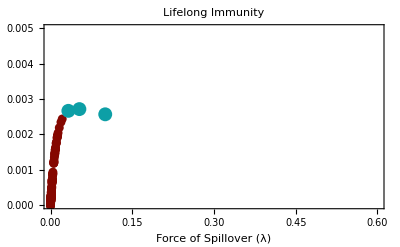

```mathematica
RealizedBurdenWanelessCompiled=Show[{RealizedBurdenPlotWaneless,RealizedTheoBurdenPlotWaneless}]
```

#### Lifelong Immunity with α estimated from the Illori et al. (2019) data increased by 50%

```mathematica
Module[{i,j},Burden={};For[i=1,i≤Length[ForceNoWane],i++,ThisLambda=ForceNoWane[[i]];MySols=NDSolve[{S'[a]==-λ S[a]-δ S[a],Ι'[a]==λ S[a]-γ Ι[a]-(μo+α a) Ι[a]-δ Ι[a],M'[a]==(μo+α a) Ι[a]-v M[a]-δ M[a]-γ M[a],R'[a]==γ(Ι[a]+M[a])-δ R[a],S[0]==b,Ι[0]==0,M[0]==0,R[0]==0}//.LassaParsWaneless/.IlloriFitPlus50/.λ->ThisLambda,{S[a],Ι[a],M[a],R[a]},{a,MaxAge}];Ν=NIntegrate[(S[a]+Ι[a]+M[a]+R[a])/.MySols,{a,0,MaxAge},AccuracyGoal->8];ℬ=NIntegrate[(1/Ν(μo+α a) Ι[a]/.MySols)//.LassaParsWaneless/.IlloriFitPlus50/.λ->ThisLambda,{a,0,MaxAge},AccuracyGoal->8];Burden=Append[Burden,Flatten[ {ThisLambda,ℬ}]]]]
```

```mathematica
Module[{i,j},TheoBurden={};For[i=1,i≤Length[TheoreticalForceNoWane],i++,ThisLambda=TheoreticalForceNoWane[[i]];MySols=NDSolve[{S'[a]==-λ S[a]-δ S[a],Ι'[a]==λ S[a]-γ Ι[a]-(μo+α a) Ι[a]-δ Ι[a],M'[a]==(μo+α a) Ι[a]-v M[a]-δ M[a]-γ M[a],R'[a]==γ(Ι[a]+M[a])-δ R[a],S[0]==b,Ι[0]==0,M[0]==0,R[0]==0}//.LassaParsWaneless/.IlloriFitPlus50/.λ->ThisLambda,{S[a],Ι[a],M[a],R[a]},{a,MaxAge}];Ν=NIntegrate[(S[a]+Ι[a]+M[a]+R[a])/.MySols,{a,0,MaxAge},AccuracyGoal->8];ℬ=NIntegrate[(1/Ν(μo+α a) Ι[a]/.MySols)//.LassaParsWaneless/.IlloriFitPlus50/.λ->ThisLambda,{a,0,MaxAge},AccuracyGoal->8];TheoBurden=Append[TheoBurden,Flatten[ {ThisLambda,ℬ}]]]]
```

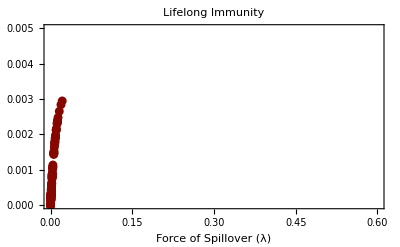

```mathematica
RealizedBurdenPlotWaneless=ListPlot[Burden,PlotRange->{{0,0.6},{0,0.005}},PlotLabel->"Lifelong Immunity",LabelStyle->Black,PlotStyle->{CMYKColor[0.07,0.95,1,0.44],PointSize->.016},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Force of Spillover (λ)",""},BaseStyle->{FontSize->14},ImageSize->400]
```

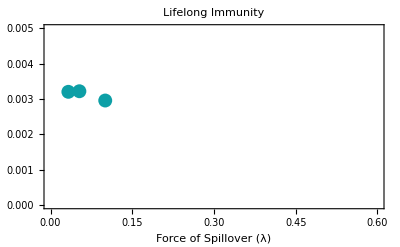

```mathematica
RealizedTheoBurdenPlotWaneless=ListPlot[TheoBurden,PlotRange->{{0,0.6},{0,0.005}},PlotLabel->"Lifelong Immunity",LabelStyle->Black,PlotStyle->{CMYKColor[0.93,0.17,0.13,0.25],PointSize->.025},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Force of Spillover (λ)",""},BaseStyle->{FontSize->14},ImageSize->400]
```

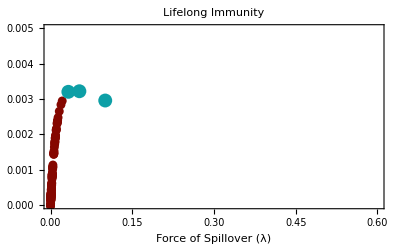

```mathematica
RealizedBurdenWanelessCompiledPlus50=Show[{RealizedBurdenPlotWaneless,RealizedTheoBurdenPlotWaneless}]
```

#### Lifelong Immunity with α estimated from the Illori et al. (2019) data increased by 100%

```mathematica
Module[{i,j},Burden={};For[i=1,i≤Length[ForceNoWane],i++,ThisLambda=ForceNoWane[[i]];MySols=NDSolve[{S'[a]==-λ S[a]-δ S[a],Ι'[a]==λ S[a]-γ Ι[a]-(μo+α a) Ι[a]-δ Ι[a],M'[a]==(μo+α a) Ι[a]-v M[a]-δ M[a]-γ M[a],R'[a]==γ(Ι[a]+M[a])-δ R[a],S[0]==b,Ι[0]==0,M[0]==0,R[0]==0}//.LassaParsWaneless/.IlloriFitPlus100/.λ->ThisLambda,{S[a],Ι[a],M[a],R[a]},{a,MaxAge}];Ν=NIntegrate[(S[a]+Ι[a]+M[a]+R[a])/.MySols,{a,0,MaxAge},AccuracyGoal->8];ℬ=NIntegrate[(1/Ν(μo+α a) Ι[a]/.MySols)//.LassaParsWaneless/.IlloriFitPlus100/.λ->ThisLambda,{a,0,MaxAge},AccuracyGoal->8];Burden=Append[Burden,Flatten[ {ThisLambda,ℬ}]]]]
```

```mathematica
Module[{i,j},TheoBurden={};For[i=1,i≤Length[TheoreticalForceNoWane],i++,ThisLambda=TheoreticalForceNoWane[[i]];MySols=NDSolve[{S'[a]==-λ S[a]-δ S[a],Ι'[a]==λ S[a]-γ Ι[a]-(μo+α a) Ι[a]-δ Ι[a],M'[a]==(μo+α a) Ι[a]-v M[a]-δ M[a]-γ M[a],R'[a]==γ(Ι[a]+M[a])-δ R[a],S[0]==b,Ι[0]==0,M[0]==0,R[0]==0}//.LassaParsWaneless/.IlloriFitPlus100/.λ->ThisLambda,{S[a],Ι[a],M[a],R[a]},{a,MaxAge},AccuracyGoal->8];Ν=NIntegrate[(S[a]+Ι[a]+M[a]+R[a])/.MySols,{a,0,MaxAge}];ℬ=NIntegrate[(1/Ν(μo+α a) Ι[a]/.MySols)//.LassaParsWaneless/.IlloriFitPlus100/.λ->ThisLambda,{a,0,MaxAge},AccuracyGoal->8];TheoBurden=Append[TheoBurden,Flatten[ {ThisLambda,ℬ}]]]]
```

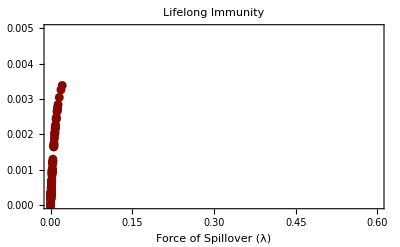

```mathematica
RealizedBurdenPlotWaneless=ListPlot[Burden,PlotRange->{{0,0.6},{0,0.005}},PlotLabel->"Lifelong Immunity",LabelStyle->Black,PlotStyle->{CMYKColor[0.07,0.95,1,0.44],PointSize->.016},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Force of Spillover (λ)",""},BaseStyle->{FontSize->14},ImageSize->400]
```

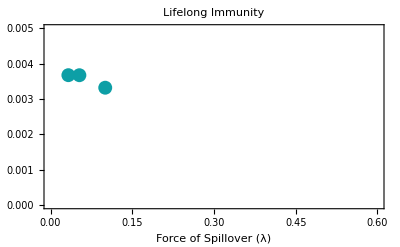

```mathematica
RealizedTheoBurdenPlotWaneless=ListPlot[TheoBurden,PlotRange->{{0,0.6},{0,0.005}},PlotLabel->"Lifelong Immunity",LabelStyle->Black,PlotStyle->{CMYKColor[0.93,0.17,0.13,0.25],PointSize->.025},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Force of Spillover (λ)",""},BaseStyle->{FontSize->14},ImageSize->400]
```

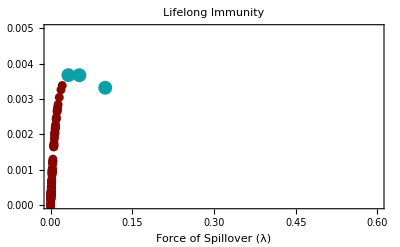

```mathematica
RealizedBurdenWanelessCompiledPlus100=Show[{RealizedBurdenPlotWaneless,RealizedTheoBurdenPlotWaneless}]
```

#### Waning Immunity with α estimated from the Illori et al. (2019) data

```mathematica
Module[{i,j},Burden={};For[i=1,i≤Length[ForceWane],i++,ThisLambda=ForceWane[[i]];MySols=NDSolve[{S'[a]==-λ S[a]-δ S[a]+ω R[a],Ι'[a]==λ S[a]-γ Ι[a]-(μo+α a) Ι[a]-δ Ι[a],M'[a]==(μo+α a) Ι[a]-v M[a]-δ M[a]-γ M[a],R'[a]==γ(Ι[a]+M[a])-ω R[a]-δ R[a],S[0]==b,Ι[0]==0,M[0]==0,R[0]==0}//.LassaParsWaning/.IlloriFit/.λ->ThisLambda,{S[a],Ι[a],M[a],R[a]},{a,MaxAge}];Ν=NIntegrate[(S[a]+Ι[a]+M[a]+R[a])/.MySols,{a,0,MaxAge},AccuracyGoal->8];ℬ=NIntegrate[(1/Ν(μo+α a) Ι[a]/.MySols)//.LassaParsWaning/.IlloriFit/.λ->ThisLambda,{a,0,MaxAge},AccuracyGoal->8];Burden=Append[Burden,Flatten[ {ThisLambda,ℬ}]]]]
```

```mathematica
Module[{i,j},TheoBurden={};For[i=1,i≤Length[TheoreticalForceWane],i++,ThisLambda=TheoreticalForceWane[[i]];MySols=NDSolve[{S'[a]==-λ S[a]-δ S[a]+ω R[a],Ι'[a]==λ S[a]-γ Ι[a]-(μo+α a) Ι[a]-δ Ι[a],M'[a]==(μo+α a) Ι[a]-v M[a]-δ M[a]-γ M[a],R'[a]==γ(Ι[a]+M[a])-ω R[a]-δ R[a],S[0]==b,Ι[0]==0,M[0]==0,R[0]==0}//.LassaParsWaning/.IlloriFit/.λ->ThisLambda,{S[a],Ι[a],M[a],R[a]},{a,MaxAge}];Ν=NIntegrate[(S[a]+Ι[a]+M[a]+R[a])/.MySols,{a,0,MaxAge},AccuracyGoal->8];ℬ=NIntegrate[(1/Ν(μo+α a) Ι[a]/.MySols)//.LassaParsWaning/.IlloriFit/.λ->ThisLambda,{a,0,MaxAge},AccuracyGoal->8];TheoBurden=Append[TheoBurden,Flatten[ {ThisLambda,ℬ}]]]]
```

```mathematica
TheoBurden
```

{{0.161244,0.0128753},{0.26248,0.0144885},{0.504882,0.0159866}}

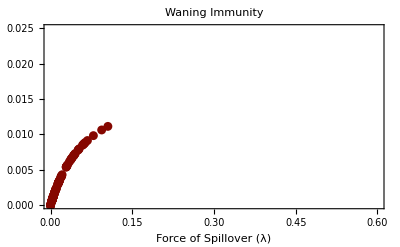

```mathematica
RealizedBurdenPlotWaning=ListPlot[Burden,PlotRange->{{0,0.6},{0,0.025}},PlotLabel->"Waning Immunity",LabelStyle->Black,PlotStyle->{CMYKColor[0.07,0.95,1,0.44],PointSize->.016},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Force of Spillover (λ)",""},BaseStyle->{FontSize->14},ImageSize->400]
```

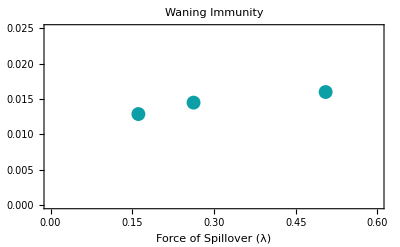

```mathematica
RealizedTheoBurdenPlotWaning=ListPlot[TheoBurden,PlotRange->{{0,0.6},{0,0.025}},PlotLabel->"Waning Immunity",LabelStyle->Black,PlotStyle->{CMYKColor[0.93,0.17,0.13,0.25],PointSize->.025},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Force of Spillover (λ)",""},BaseStyle->{FontSize->14},ImageSize->400]
```

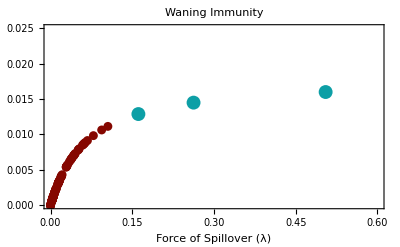

```mathematica
RealizedBurdenWaningCompiled=Show[{RealizedBurdenPlotWaning,RealizedTheoBurdenPlotWaning}]
```

#### Waning Immunity with α estimated from the Illori et al. (2019) data increased by 50%

```mathematica
Module[{i,j},Burden={};For[i=1,i≤Length[ForceWane],i++,ThisLambda=ForceWane[[i]];MySols=NDSolve[{S'[a]==-λ S[a]-δ S[a]+ω R[a],Ι'[a]==λ S[a]-γ Ι[a]-(μo+α a) Ι[a]-δ Ι[a],M'[a]==(μo+α a) Ι[a]-v M[a]-δ M[a]-γ M[a],R'[a]==γ(Ι[a]+M[a])-ω R[a]-δ R[a],S[0]==b,Ι[0]==0,M[0]==0,R[0]==0}//.LassaParsWaning/.IlloriFitPlus50/.λ->ThisLambda,{S[a],Ι[a],M[a],R[a]},{a,MaxAge}];Ν=NIntegrate[(S[a]+Ι[a]+M[a]+R[a])/.MySols,{a,0,MaxAge},AccuracyGoal->8];ℬ=NIntegrate[(1/Ν(μo+α a) Ι[a]/.MySols)//.LassaParsWaning/.IlloriFitPlus50/.λ->ThisLambda,{a,0,MaxAge},AccuracyGoal->8];Burden=Append[Burden,Flatten[ {ThisLambda,ℬ}]]]]
```

```mathematica
Module[{i,j},TheoBurden={};For[i=1,i≤Length[TheoreticalForceWane],i++,ThisLambda=TheoreticalForceWane[[i]];MySols=NDSolve[{S'[a]==-λ S[a]-δ S[a]+ω R[a],Ι'[a]==λ S[a]-γ Ι[a]-(μo+α a) Ι[a]-δ Ι[a],M'[a]==(μo+α a) Ι[a]-v M[a]-δ M[a]-γ M[a],R'[a]==γ(Ι[a]+M[a])-ω R[a]-δ R[a],S[0]==b,Ι[0]==0,M[0]==0,R[0]==0}//.LassaParsWaning/.IlloriFitPlus50/.λ->ThisLambda,{S[a],Ι[a],M[a],R[a]},{a,MaxAge}];Ν=NIntegrate[(S[a]+Ι[a]+M[a]+R[a])/.MySols,{a,0,MaxAge}];ℬ=NIntegrate[(1/Ν(μo+α a) Ι[a]/.MySols)//.LassaParsWaning/.IlloriFitPlus50/.λ->ThisLambda,{a,0,MaxAge},AccuracyGoal->8];TheoBurden=Append[TheoBurden,Flatten[ {ThisLambda,ℬ}]]]]
```

```mathematica
TheoBurden
```

{{0.161244,0.0154094},{0.26248,0.0172674},{0.504882,0.0189595}}

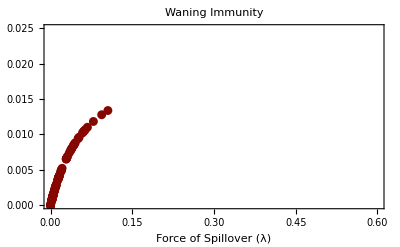

```mathematica
RealizedBurdenPlotWaning=ListPlot[Burden,PlotRange->{{0,0.6},{0,0.025}},PlotLabel->"Waning Immunity",LabelStyle->Black,PlotStyle->{CMYKColor[0.07,0.95,1,0.44],PointSize->.016},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Force of Spillover (λ)",""},BaseStyle->{FontSize->14},ImageSize->400]
```

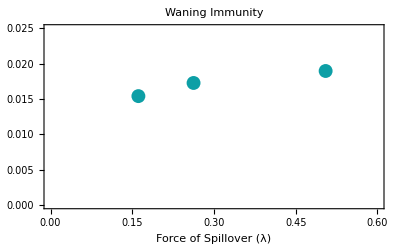

```mathematica
RealizedTheoBurdenPlotWaning=ListPlot[TheoBurden,PlotRange->{{0,0.6},{0,0.025}},PlotLabel->"Waning Immunity",LabelStyle->Black,PlotStyle->{CMYKColor[0.93,0.17,0.13,0.25],PointSize->.025},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Force of Spillover (λ)",""},BaseStyle->{FontSize->14},ImageSize->400]
```

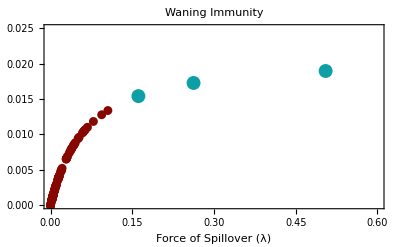

```mathematica
RealizedBurdenWaningCompiledPlus50=Show[{RealizedBurdenPlotWaning,RealizedTheoBurdenPlotWaning}]
```

#### Waning Immunity with α estimated from the Illori et al. (2019) data increased by 100%

```mathematica
Module[{i,j},Burden={};For[i=1,i≤Length[ForceWane],i++,ThisLambda=ForceWane[[i]];MySols=NDSolve[{S'[a]==-λ S[a]-δ S[a]+ω R[a],Ι'[a]==λ S[a]-γ Ι[a]-(μo+α a) Ι[a]-δ Ι[a],M'[a]==(μo+α a) Ι[a]-v M[a]-δ M[a]-γ M[a],R'[a]==γ(Ι[a]+M[a])-ω R[a]-δ R[a],S[0]==b,Ι[0]==0,M[0]==0,R[0]==0}//.LassaParsWaning/.IlloriFitPlus100/.λ->ThisLambda,{S[a],Ι[a],M[a],R[a]},{a,MaxAge}];Ν=NIntegrate[(S[a]+Ι[a]+M[a]+R[a])/.MySols,{a,0,MaxAge},AccuracyGoal->8];ℬ=NIntegrate[(1/Ν(μo+α a) Ι[a]/.MySols)//.LassaParsWaning/.IlloriFitPlus100/.λ->ThisLambda,{a,0,MaxAge},AccuracyGoal->8];Burden=Append[Burden,Flatten[ {ThisLambda,ℬ}]]]]
```

```mathematica
Module[{i,j},TheoBurden={};For[i=1,i≤Length[TheoreticalForceWane],i++,ThisLambda=TheoreticalForceWane[[i]];MySols=NDSolve[{S'[a]==-λ S[a]-δ S[a]+ω R[a],Ι'[a]==λ S[a]-γ Ι[a]-(μo+α a) Ι[a]-δ Ι[a],M'[a]==(μo+α a) Ι[a]-v M[a]-δ M[a]-γ M[a],R'[a]==γ(Ι[a]+M[a])-ω R[a]-δ R[a],S[0]==b,Ι[0]==0,M[0]==0,R[0]==0}//.LassaParsWaning/.IlloriFitPlus100/.λ->ThisLambda,{S[a],Ι[a],M[a],R[a]},{a,MaxAge}];Ν=NIntegrate[(S[a]+Ι[a]+M[a]+R[a])/.MySols,{a,0,MaxAge}];ℬ=NIntegrate[(1/Ν(μo+α a) Ι[a]/.MySols)//.LassaParsWaning/.IlloriFitPlus100/.λ->ThisLambda,{a,0,MaxAge},AccuracyGoal->8];TheoBurden=Append[TheoBurden,Flatten[ {ThisLambda,ℬ}]]]]
```

```mathematica
TheoBurden
```

{{0.161244,0.0174949},{0.26248,0.0195494},{0.504882,0.0213909}}

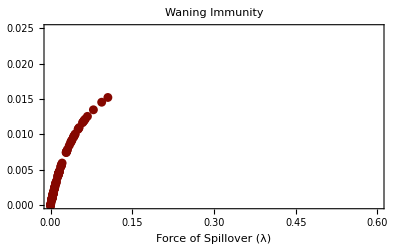

```mathematica
RealizedBurdenPlotWaning=ListPlot[Burden,PlotRange->{{0,0.6},{0,0.025}},PlotLabel->"Waning Immunity",LabelStyle->Black,PlotStyle->{CMYKColor[0.07,0.95,1,0.44],PointSize->.016},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Force of Spillover (λ)",""},BaseStyle->{FontSize->14},ImageSize->400]
```

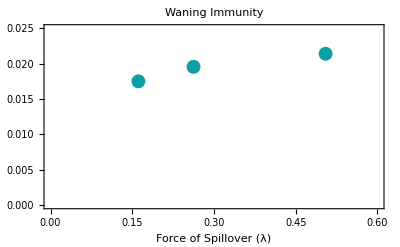

```mathematica
RealizedTheoBurdenPlotWaning=ListPlot[TheoBurden,PlotRange->{{0,0.6},{0,0.025}},PlotLabel->"Waning Immunity",LabelStyle->Black,PlotStyle->{CMYKColor[0.93,0.17,0.13,0.25],PointSize->.025},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Force of Spillover (λ)",""},BaseStyle->{FontSize->14},ImageSize->400]
```

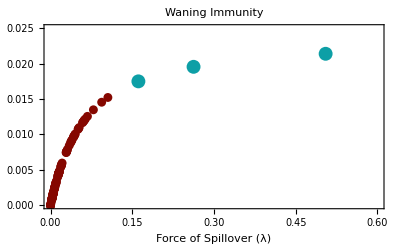

```mathematica
RealizedBurdenWaningCompiledPlus100=Show[{RealizedBurdenPlotWaning,RealizedTheoBurdenPlotWaning}]
```

### Finally, overlay the force of infection for specific sites in West Africa onto the theoretical curves

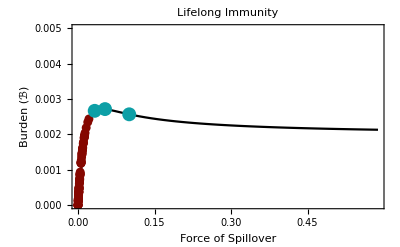

```mathematica
WanelessPlot=Show[{NoWaneBurdenPlot,RealizedBurdenWanelessCompiled}]
```

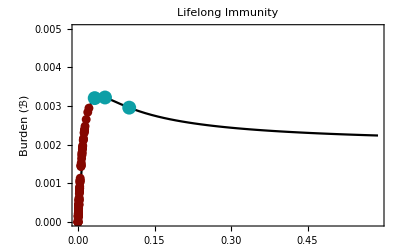

```mathematica
WanelessPlotPlus50=Show[{NoWaneBurdenPlotPlus50,RealizedBurdenWanelessCompiledPlus50}]
```

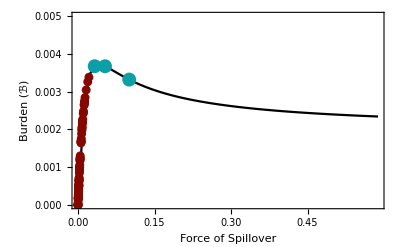

```mathematica
WanelessPlotPlus100=Show[{NoWaneBurdenPlotPlus100,RealizedBurdenWanelessCompiledPlus100}]
```

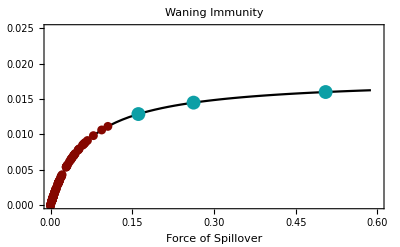

```mathematica
WaningPlot=Show[{WaneBurdenPlot,RealizedBurdenWaningCompiled}]
```

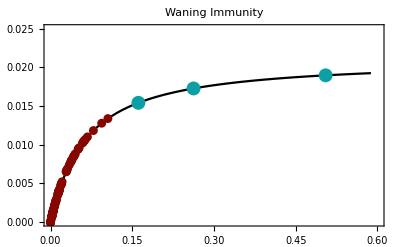

```mathematica
WaningPlotPlus50=Show[{WaneBurdenPlotPlus50,RealizedBurdenWaningCompiledPlus50}]
```

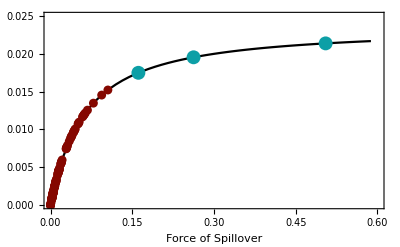

```mathematica
WaningPlotPlus100=Show[{WaneBurdenPlotPlus100,RealizedBurdenWaningCompiledPlus100}]
```

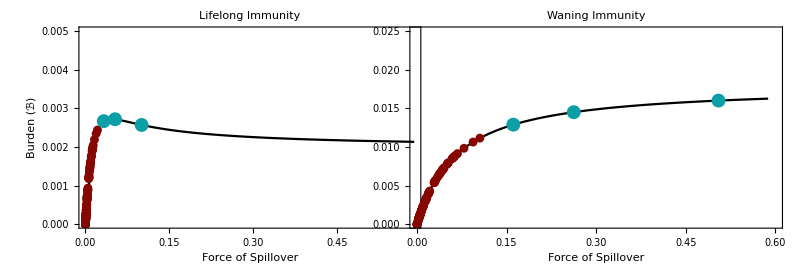

```mathematica
Figure5=GraphicsRow[{WanelessPlot,WaningPlot},ImageSize->800,Spacings->-70]
```

```mathematica
Export[HomePath<>"\\Figure5.png",Figure5,ImageResolution->400]
```

C:\Work\Current Projects\Porous Spillover Prevention\Figures\Figure5.png

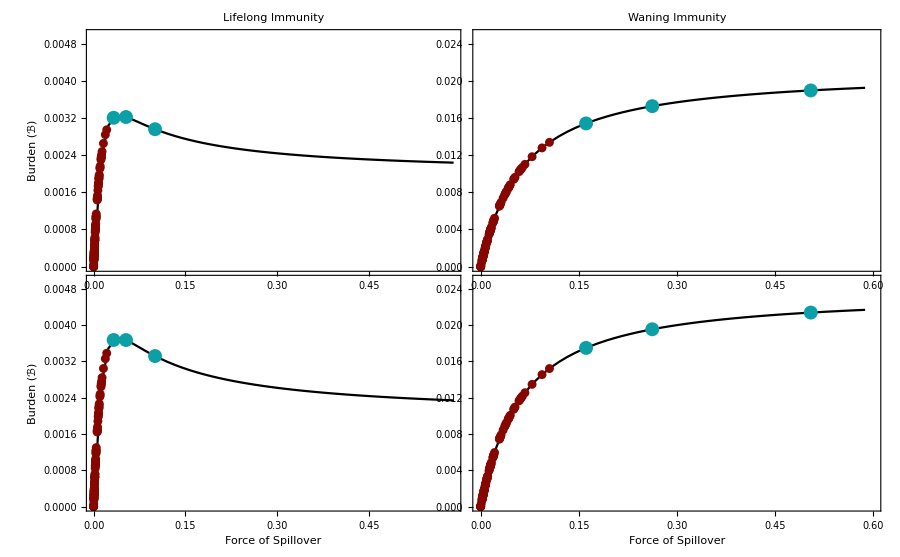

```mathematica
FigureA2=GraphicsGrid[{{WanelessPlotPlus50,WaningPlotPlus50},{WanelessPlotPlus100,WaningPlotPlus100}},ImageSize->900,Spacings->{-50,-30}]
```

```mathematica
Export[HomePath<>"\\FigureA2.png",FigureA2,ImageResolution->400]
```

C:\Work\Current Projects\Porous Spillover Prevention\Figures\FigureA2.png